```mathematica
eme=10;
ege=20;
ete =1;
gr=GridGraph[{eme,ege,ete},DirectedEdges->True];
{timegridata,d2egrid}=AbsoluteTiming@D2E[
AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0},(*SwitchingCostsData=*){}}]
];
```

460.228

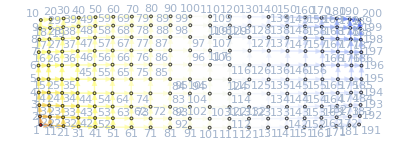

{u1→6272140902146764015104380089270033/401834757317254940707230891870852,u2→6272140902146764015104380089270033/401834757317254940707230891870852,u3→165954908340732357059304904821805/12176810827795604263855481571844,u4→165954908340732357059304904821805/12176810827795604263855481571844,u5→910316393207881639362633781889957/73060864966773625583132889431064,u6→910316393207881639362633781889957/73060864966773625583132889431064,u7→3129859714117184809142313117330593/267889838211503293804820594580568,u8→3129859714117184809142313117330593/267889838211503293804820594580568,u9→30599934720932174532623651/2748708532996949198852616,u10→30599934720932174532623651/2748708532996949198852616,u11→2681269549184331249080029/249882593908813563532056,u12→2681269549184331249080029/249882593908813563532056,u13→254173649319947272240168313973279/24353621655591208527710963143688,u14→254173649319947272240168313973279/24353621655591208527710963143688,u15→8221979621655133626859838790641611/803669514634509881414461783741704,u16→8221979621655133626859838790641611/803669514634509881414461783741704,u17→18498439164182656107581828635/1831750439059018200623739091,u18→18498439164182656107581828635/1831750439059018200623739091,u19→388144474423493710754/38681123936157106923,u20→5460430799780340484422774751937093/401834757317254940707230891870852,u21→5460430799780340484422774751937093/401834757317254940707230891870852,u22→3433769907294926878181546458462599/267889838211503293804820594580568,u23→3433769907294926878181546458462599/267889838211503293804820594580568,u24→13034728337392747453798187812013/1080200960530255216954921752341,u25→13034728337392747453798187812013/1080200960530255216954921752341,u26→3069474885570671887533709262739397/267889838211503293804820594580568,u27→3069474885570671887533709262739397/267889838211503293804820594580568,u28→8827450013261515305720973011725767/803669514634509881414461783741704,u29→8827450013261515305720973011725767/803669514634509881414461783741704,u30→8535841666050127510156457883470107/803669514634509881414461783741704,u31→8535841666050127510156457883470107/803669514634509881414461783741704,u32→2772581160488289099330860218509233/267889838211503293804820594580568,u33→2772581160488289099330860218509233/267889838211503293804820594580568,u34→43882415294392395835425162302001/4320803842121020867819687009364,u35→43882415294392395835425162302001/4320803842121020867819687009364,u36→141436183642293159549920879482181/14099465169026489147622136556872,u37→141436183642293159549920879482181/14099465169026489147622136556872,u38→54788522131715229705115634203/5495251317177054601871217273,u39→9916993272503734241783248957694695/803669514634509881414461783741704,u40→9916993272503734241783248957694695/803669514634509881414461783741704,u41→1204189431808737737224129068412525/100458689329313735176807722967713,u42→1204189431808737737224129068412525/100458689329313735176807722967713,u43→9268136828197322092368668164155173/803669514634509881414461783741704,u44→9268136828197322092368668164155173/803669514634509881414461783741704,u45→4459415794107394405815373528508773/401834757317254940707230891870852,u46→4459415794107394405815373528508773/401834757317254940707230891870852,u47→8618701285227968463435587708247151/803669514634509881414461783741704,u48→8618701285227968463435587708247151/803669514634509881414461783741704,u49→8374704989919348409988034229441651/803669514634509881414461783741704,u50→8374704989919348409988034229441651/803669514634509881414461783741704,u51→1023159073436762009062403773668787/100458689329313735176807722967713,u52→1023159073436762009062403773668787/100458689329313735176807722967713,u53→8046931408297231482358411176035117/803669514634509881414461783741704,u54→8046931408297231482358411176035117/803669514634509881414461783741704,u55→3978264824158305283407123620105149/401834757317254940707230891870852,u56→3978264824158305283407123620105149/401834757317254940707230891870852,u57→7911877397861934554806447135499323/803669514634509881414461783741704,u58→1392791574054311655113003910633/121712784285099179375202450968,u59→1392791574054311655113003910633/121712784285099179375202450968,u60→9047621995293770622475573691963135/803669514634509881414461783741704,u61→9047621995293770622475573691963135/803669514634509881414461783741704,u62→4411181193542196777212520660082637/401834757317254940707230891870852,u63→4411181193542196777212520660082637/401834757317254940707230891870852,u64→8580063582721849028117604567449669/803669514634509881414461783741704,u65→8580063582721849028117604567449669/803669514634509881414461783741704,u66→11228250738597071675272307170435/1080200960530255216954921752341,u67→11228250738597071675272307170435/1080200960530255216954921752341,u68→43865615166156997816456242670425/4320803842121020867819687009364,u69→43865615166156997816456242670425/4320803842121020867819687009364,u70→8001710470294937099657894696396717/803669514634509881414461783741704,u71→8001710470294937099657894696396717/803669514634509881414461783741704,u72→985474269077654208091385885800961/100458689329313735176807722967713,u73→985474269077654208091385885800961/100458689329313735176807722967713,u74→7805447319496566135746640518822435/803669514634509881414461783741704,u75→7805447319496566135746640518822435/803669514634509881414461783741704,u76→1176191240428608841994751309309/121712784285099179375202450968,u77→2896349614196179292243588739/269873135887137870011535368,u78→2896349614196179292243588739/269873135887137870011535368,u79→8538007376140167178973056078477367/803669514634509881414461783741704,u80→8538007376140167178973056078477367/803669514634509881414461783741704,u81→8393627142124632474738318857093119/803669514634509881414461783741704,u82→8393627142124632474738318857093119/803669514634509881414461783741704,u83→93468656887181732045591288156957/9132608120846703197891611178883,u84→93468656887181732045591288156957/9132608120846703197891611178883,u85→3938174442429064623751873278015/392800349283729169801789728124,u86→3938174442429064623751873278015/392800349283729169801789728124,u87→10626053325121370348649084793218/1080200960530255216954921752341,u88→10626053325121370348649084793218/1080200960530255216954921752341,u89→3889385360079608533770200186564917/401834757317254940707230891870852,u90→3889385360079608533770200186564917/401834757317254940707230891870852,u91→36751614413378947086896660068787/3845308682461769767533309970056,u92→36751614413378947086896660068787/3845308682461769767533309970056,u93→692279519681665102522716804845857/73060864966773625583132889431064,u94→692279519681665102522716804845857/73060864966773625583132889431064,u95→69258872905392513284309279/7341382730267156003088392,u96→18050928887610370505409744008485/1781972316262771355686168034904,u97→18050928887610370505409744008485/1781972316262771355686168034904,u98→8085587344497910906803659948781947/803669514634509881414461783741704,u99→8085587344497910906803659948781947/803669514634509881414461783741704,u100→7988896999201976745543144671917619/803669514634509881414461783741704,u101→7988896999201976745543144671917619/803669514634509881414461783741704,u102→357716890465073725317994421813063/36530432483386812791566444715532,u103→357716890465073725317994421813063/36530432483386812791566444715532,u104→88013359174556268124724794642099/9132608120846703197891611178883,u105→88013359174556268124724794642099/9132608120846703197891611178883,u106→3813927322643456637991041053984597/401834757317254940707230891870852,u107→3813927322643456637991041053984597/401834757317254940707230891870852,u108→940812665506928961243423219448993/100458689329313735176807722967713,u109→940812665506928961243423219448993/100458689329313735176807722967713,u110→35630191676105420596288208156287/3845308682461769767533309970056,u111→35630191676105420596288208156287/3845308682461769767533309970056,u112→671992415437153324870050537112597/73060864966773625583132889431064,u113→671992415437153324870050537112597/73060864966773625583132889431064,u114→444181025141867137349755434385/48475150167954031088392652376,u115→7712126417794565675141051878626991/803669514634509881414461783741704,u116→7712126417794565675141051878626991/803669514634509881414461783741704,u117→2558158691445740868252881498968689/267889838211503293804820594580568,u118→2558158691445740868252881498968689/267889838211503293804820594580568,u119→10223927311765781779078928228371/1080200960530255216954921752341,u120→10223927311765781779078928228371/1080200960530255216954921752341,u121→2506590649430522355817516387104999/267889838211503293804820594580568,u122→2506590649430522355817516387104999/267889838211503293804820594580568,u123→3712785642357702463364417799671789/401834757317254940707230891870852,u124→3712785642357702463364417799671789/401834757317254940707230891870852,u125→916744746980121284951280207703241/100458689329313735176807722967713,u126→916744746980121284951280207703241/100458689329313735176807722967713,u127→2417556623489854503880941678868255/267889838211503293804820594580568,u128→2417556623489854503880941678868255/267889838211503293804820594580568,u129→38641585671848459214073109679833/4320803842121020867819687009364,u130→38641585671848459214073109679833/4320803842121020867819687009364,u131→2380601428867793997262169309438981/267889838211503293804820594580568,u132→2380601428867793997262169309438981/267889838211503293804820594580568,u133→7118467513380547376273289099987955/803669514634509881414461783741704,u134→7320934250734197322724716591148171/803669514634509881414461783741704,u135→7320934250734197322724716591148171/803669514634509881414461783741704,u136→1215598102517112032242523926384551/133944919105751646902410297290284,u137→1215598102517112032242523926384551/133944919105751646902410297290284,u138→7243262657984200156784552077493413/803669514634509881414461783741704,u139→7243262657984200156784552077493413/803669514634509881414461783741704,u140→299047624927729155935448381838375/33486229776437911725602574322571,u141→299047624927729155935448381838375/33486229776437911725602574322571,u142→100047600103776489646151685153925/11319288938514223681893827940024,u143→100047600103776489646151685153925/11319288938514223681893827940024,u144→99010367646366188789960900036425/11319288938514223681893827940024,u145→99010367646366188789960900036425/11319288938514223681893827940024,u146→1160480874503006443866012388125375/133944919105751646902410297290284,u147→1160480874503006443866012388125375/133944919105751646902410297290284,u148→6908155522476275247216825132210061/803669514634509881414461783741704,u149→6908155522476275247216825132210061/803669514634509881414461783741704,u150→286229088677520025145191179358013/33486229776437911725602574322571,u151→286229088677520025145191179358013/33486229776437911725602574322571,u152→6849521037711244866911764024978007/803669514634509881414461783741704,u153→47570481095846466957346113017/5495251317177054601871217273,u154→47570481095846466957346113017/5495251317177054601871217273,u155→2311893825785022896517553689227191/267889838211503293804820594580568,u156→2311893825785022896517553689227191/267889838211503293804820594580568,u157→3447858549307443523798790492818661/401834757317254940707230891870852,u158→3447858549307443523798790492818661/401834757317254940707230891870852,u159→2280719259806033660229724590582305/267889838211503293804820594580568,u160→2280719259806033660229724590582305/267889838211503293804820594580568,u161→95508000614079140651271238276957/11319288938514223681893827940024,u162→95508000614079140651271238276957/11319288938514223681893827940024,u163→94629881427336026882617041887857/11319288938514223681893827940024,u164→94629881427336026882617041887857/11319288938514223681893827940024,u165→2220326497411438829945807747869333/267889838211503293804820594580568,u166→2220326497411438829945807747869333/267889838211503293804820594580568,u167→826612972457846038546129936880843/100458689329313735176807722967713,u168→826612972457846038546129936880843/100458689329313735176807722967713,u169→115412485372824917684618528646741/14099465169026489147622136556872,u170→115412485372824917684618528646741/14099465169026489147622136556872,u171→3280298735746353310488707335176877/401834757317254940707230891870852,u172→45228977010467126295446675173/5495251317177054601871217273,u173→45228977010467126295446675173/5495251317177054601871217273,u174→1366780146881544801768843747/166522767187183472783976281,u175→1366780146881544801768843747/166522767187183472783976281,u176→6414238983091083444148521041669/785600698567458339603579456248,u177→6414238983091083444148521041669/785600698567458339603579456248,u178→2171567659064132715489365006521797/267889838211503293804820594580568,u179→2171567659064132715489365006521797/267889838211503293804820594580568,u180→6460013206271386290729278278942351/803669514634509881414461783741704,u181→6460013206271386290729278278942351/803669514634509881414461783741704,u182→582100244239772432227121348390297/73060864966773625583132889431064,u183→582100244239772432227121348390297/73060864966773625583132889431064,u184→192406283664109123609659672018035/24353621655591208527710963143688,u185→192406283664109123609659672018035/24353621655591208527710963143688,u186→67784606856875926756974768510803/8641607684242041735639374018728,u187→67784606856875926756974768510803/8641607684242041735639374018728,u188→1045174547598020949876997010244023/133944919105751646902410297290284,u189→1045174547598020949876997010244023/133944919105751646902410297290284,u190→22010135703281773581942959/2828518506707552286637452,u191→43012705088463933470622068851/5495251317177054601871217273,u192→43012705088463933470622068851/5495251317177054601871217273,u193→3899499802766783652019967401/499568301561550418351928843,u194→3899499802766783652019967401/499568301561550418351928843,u195→567301215145824258346373337003217/73060864966773625583132889431064,u196→567301215145824258346373337003217/73060864966773625583132889431064,u197→6194874443377926951089991001944911/803669514634509881414461783741704,u198→6194874443377926951089991001944911/803669514634509881414461783741704,u199→6141179117656031275710425346246799/803669514634509881414461783741704,u200→6141179117656031275710425346246799/803669514634509881414461783741704,u201→553115327092921976316316536327065/73060864966773625583132889431064,u202→553115327092921976316316536327065/73060864966773625583132889431064,u203→548143529736466353067333196270425/73060864966773625583132889431064,u204→548143529736466353067333196270425/73060864966773625583132889431064,u205→5982515324591349666844823152912679/803669514634509881414461783741704,u206→5982515324591349666844823152912679/803669514634509881414461783741704,u207→2973974663948083306314397394134309/401834757317254940707230891870852,u208→2973974663948083306314397394134309/401834757317254940707230891870852,u209→20869375111006868741620631/2828518506707552286637452,u210→6196371410645169459972723/832235547050894230178891,u211→6196371410645169459972723/832235547050894230178891,u212→5965770138042507722185504045675829/803669514634509881414461783741704,u213→5965770138042507722185504045675829/803669514634509881414461783741704,u214→2965689012315379860919860341746661/401834757317254940707230891870852,u215→2965689012315379860919860341746661/401834757317254940707230891870852,u216→5883302312059211540371336934932067/803669514634509881414461783741704,u217→5883302312059211540371336934932067/803669514634509881414461783741704,u218→62640432504867420661752152736583/8641607684242041735639374018728,u219→62640432504867420661752152736583/8641607684242041735639374018728,u220→61970040437568914451274217858883/8641607684242041735639374018728,u221→61970040437568914451274217858883/8641607684242041735639374018728,u222→5702124024875427049519586406793151/803669514634509881414461783741704,u223→5702124024875427049519586406793151/803669514634509881414461783741704,u224→706070588209830122826397399112843/100458689329313735176807722967713,u225→706070588209830122826397399112843/100458689329313735176807722967713,u226→295189490891497860034531532150447/42298395507079467442866409670616,u227→295189490891497860034531532150447/42298395507079467442866409670616,u228→423079970088457816949175059975/60856392142549589687601225484,u229→862450517428787394108283530753/121712784285099179375202450968,u230→862450517428787394108283530753/121712784285099179375202450968,u231→2837391838016523713362085936973877/401834757317254940707230891870852,u232→2837391838016523713362085936973877/401834757317254940707230891870852,u233→5636126281817252782991935046330005/803669514634509881414461783741704,u234→5636126281817252782991935046330005/803669514634509881414461783741704,u235→697674569659436170876585731223477/100458689329313735176807722967713,u236→697674569659436170876585731223477/100458689329313735176807722967713,u237→59296190337650845442167056730687/8641607684242041735639374018728,u238→59296190337650845442167056730687/8641607684242041735639374018728,u239→58504324698122551240128930458187/8641607684242041735639374018728,u240→58504324698122551240128930458187/8641607684242041735639374018728,u241→2683569403014014143878999507209533/401834757317254940707230891870852,u242→2683569403014014143878999507209533/401834757317254940707230891870852,u243→5301019146309327873424208101046653/803669514634509881414461783741704,u244→5301019146309327873424208101046653/803669514634509881414461783741704,u245→656336648648856979594202077529095/100458689329313735176807722967713,u246→656336648648856979594202077529095/100458689329313735176807722967713,u247→791056724755312843780712340965/121712784285099179375202450968,u248→5425814290912980653935471078552111/803669514634509881414461783741704,u249→5425814290912980653935471078552111/803669514634509881414461783741704,u250→5402477517690146038422252250223123/803669514634509881414461783741704,u251→5402477517690146038422252250223123/803669514634509881414461783741704,u252→669618358666214327048895222261391/100458689329313735176807722967713,u253→669618358666214327048895222261391/100458689329313735176807722967713,u254→5291611933823964518565935141935301/803669514634509881414461783741704,u255→5291611933823964518565935141935301/803669514634509881414461783741704,u256→2605161914226278875299259258457069/401834757317254940707230891870852,u257→2605161914226278875299259258457069/401834757317254940707230891870852,u258→639838814947265387934990572399561/100458689329313735176807722967713,u259→639838814947265387934990572399561/100458689329313735176807722967713,u260→5024509856001960962756211017225069/803669514634509881414461783741704,u261→5024509856001960962756211017225069/803669514634509881414461783741704,u262→2468839942169893193287018788316021/401834757317254940707230891870852,u263→2468839942169893193287018788316021/401834757317254940707230891870852,u264→4869805729956305425450115681633999/803669514634509881414461783741704,u265→4869805729956305425450115681633999/803669514634509881414461783741704,u266→4832155386498962355067708299913075/803669514634509881414461783741704,u267→11486041216112001685337394305701/1781972316262771355686168034904,u268→11486041216112001685337394305701/1781972316262771355686168034904,u269→1717455078161613818879401423433833/267889838211503293804820594580568,u270→1717455078161613818879401423433833/267889838211503293804820594580568,u271→54812599397715001350371233052431/8641607684242041735639374018728,u272→54812599397715001350371233052431/8641607684242041735639374018728,u273→76026976973304490003960218529517/12176810827795604263855481571844,u274→76026976973304490003960218529517/12176810827795604263855481571844,u275→55868490443256985843484978074669/9132608120846703197891611178883,u276→55868490443256985843484978074669/9132608120846703197891611178883,u277→2399553098466288217616489125017677/401834757317254940707230891870852,u278→2399553098466288217616489125017677/401834757317254940707230891870852,u279→194771258919246086383870120777195/33486229776437911725602574322571,u280→194771258919246086383870120777195/33486229776437911725602574322571,u281→234366661783791289019170422731/41347405187760965242293655592,u282→234366661783791289019170422731/41347405187760965242293655592,u283→135111953327139912830457582719943/24353621655591208527710963143688,u284→135111953327139912830457582719943/24353621655591208527710963143688,u285→265595806501070687753722518289/48475150167954031088392652376,u286→11003180133041499267600485912993/1781972316262771355686168034904,u287→11003180133041499267600485912993/1781972316262771355686168034904,u288→1643069029265070634152958441745213/267889838211503293804820594580568,u289→1643069029265070634152958441745213/267889838211503293804820594580568,u290→4863194391897328089047358224163583/803669514634509881414461783741704,u291→4863194391897328089047358224163583/803669514634509881414461783741704,u292→18051178348993602131319544717463/3044202706948901065963870392961,u293→18051178348993602131319544717463/3044202706948901065963870392961,u294→2969589071961093784131780468877/514513133568828349176992179092,u295→2969589071961093784131780468877/514513133568828349176992179092,u296→7899255096978277834528921569932/1414911117314277960236728492503,u297→7899255096978277834528921569932/1414911117314277960236728492503,u298→719839999703589268366121136787975/133944919105751646902410297290284,u299→719839999703589268366121136787975/133944919105751646902410297290284,u300→19859591685018639021389671394483/3845308682461769767533309970056,u301→19859591685018639021389671394483/3845308682461769767533309970056,u302→121402255398586692461688003032203/24353621655591208527710963143688,u303→121402255398586692461688003032203/24353621655591208527710963143688,u304→236388731627310049962849892181/48475150167954031088392652376,u305→4777891043743423846517417283172739/803669514634509881414461783741704,u306→4777891043743423846517417283172739/803669514634509881414461783741704,u307→1579611494932320631487373219905877/267889838211503293804820594580568,u308→1579611494932320631487373219905877/267889838211503293804820594580568,u309→2330243825836147182738836546066189/401834757317254940707230891870852,u310→2330243825836147182738836546066189/401834757317254940707230891870852,u311→1514190444666196976850288494047783/267889838211503293804820594580568,u312→1514190444666196976850288494047783/267889838211503293804820594580568,u313→7720558773570997247091371552537/1414911117314277960236728492503,u314→7720558773570997247091371552537/1414911117314277960236728492503,u315→29510304611107793688775800308003/5659644469257111840946913970012,u316→29510304611107793688775800308003/5659644469257111840946913970012,u317→1321406073857226334030385203696799/267889838211503293804820594580568,u318→1321406073857226334030385203696799/267889838211503293804820594580568,u319→465239927151141809472964857296849/100458689329313735176807722967713,u320→465239927151141809472964857296849/100458689329313735176807722967713,u321→1165553269666585802577728828858977/267889838211503293804820594580568,u322→1165553269666585802577728828858977/267889838211503293804820594580568,u323→3347679040812908171497595356630367/803669514634509881414461783741704,u324→4632404406431593475402313043040743/803669514634509881414461783741704,u325→4632404406431593475402313043040743/803669514634509881414461783741704,u326→191156339832371560974771372430407/33486229776437911725602574322571,u327→191156339832371560974771372430407/33486229776437911725602574322571,u328→48358606408562328471509129059193/8641607684242041735639374018728,u329→48358606408562328471509129059193/8641607684242041735639374018728,u330→726501536133238659618254998198295/133944919105751646902410297290284,u331→726501536133238659618254998198295/133944919105751646902410297290284,u332→4169576814374179620220725949098415/803669514634509881414461783741704,u333→4169576814374179620220725949098415/803669514634509881414461783741704,u334→3925580519065559566773172470292915/803669514634509881414461783741704,u335→3925580519065559566773172470292915/803669514634509881414461783741704,u336→151060425669947467440750546730105/33486229776437911725602574322571,u337→151060425669947467440750546730105/33486229776437911725602574322571,u338→35227365334367805783226795853601/8641607684242041735639374018728,u339→35227365334367805783226795853601/8641607684242041735639374018728,u340→485127724970604355402621271873311/133944919105751646902410297290284,u341→485127724970604355402621271873311/133944919105751646902410297290284,u342→2627288531789793788425511220845371/803669514634509881414461783741704,u343→2265785009787219558147504453809861/401834757317254940707230891870852,u344→2265785009787219558147504453809861/401834757317254940707230891870852,u345→4482419336682817935863270048055749/803669514634509881414461783741704,u346→4482419336682817935863270048055749/803669514634509881414461783741704,u347→547769069942067800602459998795985/100458689329313735176807722967713,u348→547769069942067800602459998795985/100458689329313735176807722967713,u349→4226538322828660732216179523012367/803669514634509881414461783741704,u350→4226538322828660732216179523012367/803669514634509881414461783741704,u351→4008440138243400520052302295069959/803669514634509881414461783741704,u352→4008440138243400520052302295069959/803669514634509881414461783741704,u353→3716831791032012724487787166814299/803669514634509881414461783741704,u354→3716831791032012724487787166814299/803669514634509881414461783741704,u355→3335857147581512367607632390321875/803669514634509881414461783741704,u356→3335857147581512367607632390321875/803669514634509881414461783741704,u357→1423221960636661962291454223201197/401834757317254940707230891870852,u358→1423221960636661962291454223201197/401834757317254940707230891870852,u359→118051162232039336613901094902751/42298395507079467442866409670616,u360→118051162232039336613901094902751/42298395507079467442866409670616,u361→11100460893365017377080101435/5495251317177054601871217273,u362→57907912952619/10388394038924,u363→201281936892880579951994470722983/36530432483386812791566444715532,u364→392936562058035854849901944354405/73060864966773625583132889431064,u365→4156551376735268046283205817421859/803669514634509881414461783741704,u366→29636432090206800164265/6074733275551230105112,u367→2472018538571163187031/552248479595566373192,u368→286791151085633963889256438777117/73060864966773625583132889431064,u369→2530801479006829997219788577750539/803669514634509881414461783741704,u370→10880544375343201030404767657/5495251317177054601871217273,u371→0,u372→6272140902146764015104380089270033/401834757317254940707230891870852,u373→165954908340732357059304904821805/12176810827795604263855481571844,u374→5460430799780340484422774751937093/401834757317254940707230891870852,u375→910316393207881639362633781889957/73060864966773625583132889431064,u376→3433769907294926878181546458462599/267889838211503293804820594580568,u377→3129859714117184809142313117330593/267889838211503293804820594580568,u378→13034728337392747453798187812013/1080200960530255216954921752341,u379→30599934720932174532623651/2748708532996949198852616,u380→3069474885570671887533709262739397/267889838211503293804820594580568,u381→2681269549184331249080029/249882593908813563532056,u382→8827450013261515305720973011725767/803669514634509881414461783741704,u383→254173649319947272240168313973279/24353621655591208527710963143688,u384→8535841666050127510156457883470107/803669514634509881414461783741704,u385→8221979621655133626859838790641611/803669514634509881414461783741704,u386→2772581160488289099330860218509233/267889838211503293804820594580568,u387→18498439164182656107581828635/1831750439059018200623739091,u388→43882415294392395835425162302001/4320803842121020867819687009364,u389→388144474423493710754/38681123936157106923,u390→141436183642293159549920879482181/14099465169026489147622136556872,u391→54788522131715229705115634203/5495251317177054601871217273,u392→3433769907294926878181546458462599/267889838211503293804820594580568,u393→9916993272503734241783248957694695/803669514634509881414461783741704,u394→13034728337392747453798187812013/1080200960530255216954921752341,u395→1204189431808737737224129068412525/100458689329313735176807722967713,u396→3069474885570671887533709262739397/267889838211503293804820594580568,u397→9268136828197322092368668164155173/803669514634509881414461783741704,u398→8827450013261515305720973011725767/803669514634509881414461783741704,u399→4459415794107394405815373528508773/401834757317254940707230891870852,u400→8535841666050127510156457883470107/803669514634509881414461783741704,u401→8618701285227968463435587708247151/803669514634509881414461783741704,u402→2772581160488289099330860218509233/267889838211503293804820594580568,u403→8374704989919348409988034229441651/803669514634509881414461783741704,u404→43882415294392395835425162302001/4320803842121020867819687009364,u405→1023159073436762009062403773668787/100458689329313735176807722967713,u406→141436183642293159549920879482181/14099465169026489147622136556872,u407→8046931408297231482358411176035117/803669514634509881414461783741704,u408→54788522131715229705115634203/5495251317177054601871217273,u409→3978264824158305283407123620105149/401834757317254940707230891870852,u410→7911877397861934554806447135499323/803669514634509881414461783741704,u411→1204189431808737737224129068412525/100458689329313735176807722967713,u412→1392791574054311655113003910633/121712784285099179375202450968,u413→9268136828197322092368668164155173/803669514634509881414461783741704,u414→9047621995293770622475573691963135/803669514634509881414461783741704,u415→4459415794107394405815373528508773/401834757317254940707230891870852,u416→4411181193542196777212520660082637/401834757317254940707230891870852,u417→8618701285227968463435587708247151/803669514634509881414461783741704,u418→8580063582721849028117604567449669/803669514634509881414461783741704,u419→8374704989919348409988034229441651/803669514634509881414461783741704,u420→11228250738597071675272307170435/1080200960530255216954921752341,u421→1023159073436762009062403773668787/100458689329313735176807722967713,u422→43865615166156997816456242670425/4320803842121020867819687009364,u423→8046931408297231482358411176035117/803669514634509881414461783741704,u424→8001710470294937099657894696396717/803669514634509881414461783741704,u425→3978264824158305283407123620105149/401834757317254940707230891870852,u426→985474269077654208091385885800961/100458689329313735176807722967713,u427→7911877397861934554806447135499323/803669514634509881414461783741704,u428→7805447319496566135746640518822435/803669514634509881414461783741704,u429→1176191240428608841994751309309/121712784285099179375202450968,u430→9047621995293770622475573691963135/803669514634509881414461783741704,u431→2896349614196179292243588739/269873135887137870011535368,u432→4411181193542196777212520660082637/401834757317254940707230891870852,u433→8538007376140167178973056078477367/803669514634509881414461783741704,u434→8580063582721849028117604567449669/803669514634509881414461783741704,u435→8393627142124632474738318857093119/803669514634509881414461783741704,u436→11228250738597071675272307170435/1080200960530255216954921752341,u437→93468656887181732045591288156957/9132608120846703197891611178883,u438→43865615166156997816456242670425/4320803842121020867819687009364,u439→3938174442429064623751873278015/392800349283729169801789728124,u440→8001710470294937099657894696396717/803669514634509881414461783741704,u441→10626053325121370348649084793218/1080200960530255216954921752341,u442→985474269077654208091385885800961/100458689329313735176807722967713,u443→3889385360079608533770200186564917/401834757317254940707230891870852,u444→7805447319496566135746640518822435/803669514634509881414461783741704,u445→36751614413378947086896660068787/3845308682461769767533309970056,u446→1176191240428608841994751309309/121712784285099179375202450968,u447→692279519681665102522716804845857/73060864966773625583132889431064,u448→69258872905392513284309279/7341382730267156003088392,u449→8538007376140167178973056078477367/803669514634509881414461783741704,u450→18050928887610370505409744008485/1781972316262771355686168034904,u451→8393627142124632474738318857093119/803669514634509881414461783741704,u452→8085587344497910906803659948781947/803669514634509881414461783741704,u453→93468656887181732045591288156957/9132608120846703197891611178883,u454→7988896999201976745543144671917619/803669514634509881414461783741704,u455→3938174442429064623751873278015/392800349283729169801789728124,u456→357716890465073725317994421813063/36530432483386812791566444715532,u457→10626053325121370348649084793218/1080200960530255216954921752341,u458→88013359174556268124724794642099/9132608120846703197891611178883,u459→3889385360079608533770200186564917/401834757317254940707230891870852,u460→3813927322643456637991041053984597/401834757317254940707230891870852,u461→36751614413378947086896660068787/3845308682461769767533309970056,u462→940812665506928961243423219448993/100458689329313735176807722967713,u463→692279519681665102522716804845857/73060864966773625583132889431064,u464→35630191676105420596288208156287/3845308682461769767533309970056,u465→69258872905392513284309279/7341382730267156003088392,u466→671992415437153324870050537112597/73060864966773625583132889431064,u467→444181025141867137349755434385/48475150167954031088392652376,u468→8085587344497910906803659948781947/803669514634509881414461783741704,u469→7712126417794565675141051878626991/803669514634509881414461783741704,u470→7988896999201976745543144671917619/803669514634509881414461783741704,u471→2558158691445740868252881498968689/267889838211503293804820594580568,u472→357716890465073725317994421813063/36530432483386812791566444715532,u473→10223927311765781779078928228371/1080200960530255216954921752341,u474→88013359174556268124724794642099/9132608120846703197891611178883,u475→2506590649430522355817516387104999/267889838211503293804820594580568,u476→3813927322643456637991041053984597/401834757317254940707230891870852,u477→3712785642357702463364417799671789/401834757317254940707230891870852,u478→940812665506928961243423219448993/100458689329313735176807722967713,u479→916744746980121284951280207703241/100458689329313735176807722967713,u480→35630191676105420596288208156287/3845308682461769767533309970056,u481→2417556623489854503880941678868255/267889838211503293804820594580568,u482→671992415437153324870050537112597/73060864966773625583132889431064,u483→38641585671848459214073109679833/4320803842121020867819687009364,u484→444181025141867137349755434385/48475150167954031088392652376,u485→2380601428867793997262169309438981/267889838211503293804820594580568,u486→7118467513380547376273289099987955/803669514634509881414461783741704,u487→2558158691445740868252881498968689/267889838211503293804820594580568,u488→7320934250734197322724716591148171/803669514634509881414461783741704,u489→10223927311765781779078928228371/1080200960530255216954921752341,u490→1215598102517112032242523926384551/133944919105751646902410297290284,u491→2506590649430522355817516387104999/267889838211503293804820594580568,u492→7243262657984200156784552077493413/803669514634509881414461783741704,u493→3712785642357702463364417799671789/401834757317254940707230891870852,u494→299047624927729155935448381838375/33486229776437911725602574322571,u495→916744746980121284951280207703241/100458689329313735176807722967713,u496→100047600103776489646151685153925/11319288938514223681893827940024,u497→2417556623489854503880941678868255/267889838211503293804820594580568,u498→99010367646366188789960900036425/11319288938514223681893827940024,u499→38641585671848459214073109679833/4320803842121020867819687009364,u500→1160480874503006443866012388125375/133944919105751646902410297290284,u501→2380601428867793997262169309438981/267889838211503293804820594580568,u502→6908155522476275247216825132210061/803669514634509881414461783741704,u503→7118467513380547376273289099987955/803669514634509881414461783741704,u504→286229088677520025145191179358013/33486229776437911725602574322571,u505→6849521037711244866911764024978007/803669514634509881414461783741704,u506→1215598102517112032242523926384551/133944919105751646902410297290284,u507→47570481095846466957346113017/5495251317177054601871217273,u508→7243262657984200156784552077493413/803669514634509881414461783741704,u509→2311893825785022896517553689227191/267889838211503293804820594580568,u510→299047624927729155935448381838375/33486229776437911725602574322571,u511→3447858549307443523798790492818661/401834757317254940707230891870852,u512→100047600103776489646151685153925/11319288938514223681893827940024,u513→2280719259806033660229724590582305/267889838211503293804820594580568,u514→99010367646366188789960900036425/11319288938514223681893827940024,u515→95508000614079140651271238276957/11319288938514223681893827940024,u516→1160480874503006443866012388125375/133944919105751646902410297290284,u517→94629881427336026882617041887857/11319288938514223681893827940024,u518→6908155522476275247216825132210061/803669514634509881414461783741704,u519→2220326497411438829945807747869333/267889838211503293804820594580568,u520→286229088677520025145191179358013/33486229776437911725602574322571,u521→826612972457846038546129936880843/100458689329313735176807722967713,u522→6849521037711244866911764024978007/803669514634509881414461783741704,u523→115412485372824917684618528646741/14099465169026489147622136556872,u524→3280298735746353310488707335176877/401834757317254940707230891870852,u525→2311893825785022896517553689227191/267889838211503293804820594580568,u526→45228977010467126295446675173/5495251317177054601871217273,u527→3447858549307443523798790492818661/401834757317254940707230891870852,u528→1366780146881544801768843747/166522767187183472783976281,u529→2280719259806033660229724590582305/267889838211503293804820594580568,u530→6414238983091083444148521041669/785600698567458339603579456248,u531→95508000614079140651271238276957/11319288938514223681893827940024,u532→2171567659064132715489365006521797/267889838211503293804820594580568,u533→94629881427336026882617041887857/11319288938514223681893827940024,u534→6460013206271386290729278278942351/803669514634509881414461783741704,u535→2220326497411438829945807747869333/267889838211503293804820594580568,u536→582100244239772432227121348390297/73060864966773625583132889431064,u537→826612972457846038546129936880843/100458689329313735176807722967713,u538→192406283664109123609659672018035/24353621655591208527710963143688,u539→115412485372824917684618528646741/14099465169026489147622136556872,u540→67784606856875926756974768510803/8641607684242041735639374018728,u541→3280298735746353310488707335176877/401834757317254940707230891870852,u542→1045174547598020949876997010244023/133944919105751646902410297290284,u543→22010135703281773581942959/2828518506707552286637452,u544→1366780146881544801768843747/166522767187183472783976281,u545→43012705088463933470622068851/5495251317177054601871217273,u546→6414238983091083444148521041669/785600698567458339603579456248,u547→3899499802766783652019967401/499568301561550418351928843,u548→2171567659064132715489365006521797/267889838211503293804820594580568,u549→567301215145824258346373337003217/73060864966773625583132889431064,u550→6460013206271386290729278278942351/803669514634509881414461783741704,u551→6194874443377926951089991001944911/803669514634509881414461783741704,u552→582100244239772432227121348390297/73060864966773625583132889431064,u553→6141179117656031275710425346246799/803669514634509881414461783741704,u554→192406283664109123609659672018035/24353621655591208527710963143688,u555→553115327092921976316316536327065/73060864966773625583132889431064,u556→67784606856875926756974768510803/8641607684242041735639374018728,u557→548143529736466353067333196270425/73060864966773625583132889431064,u558→1045174547598020949876997010244023/133944919105751646902410297290284,u559→5982515324591349666844823152912679/803669514634509881414461783741704,u560→22010135703281773581942959/2828518506707552286637452,u561→2973974663948083306314397394134309/401834757317254940707230891870852,u562→20869375111006868741620631/2828518506707552286637452,u563→3899499802766783652019967401/499568301561550418351928843,u564→6196371410645169459972723/832235547050894230178891,u565→567301215145824258346373337003217/73060864966773625583132889431064,u566→5965770138042507722185504045675829/803669514634509881414461783741704,u567→6194874443377926951089991001944911/803669514634509881414461783741704,u568→2965689012315379860919860341746661/401834757317254940707230891870852,u569→6141179117656031275710425346246799/803669514634509881414461783741704,u570→5883302312059211540371336934932067/803669514634509881414461783741704,u571→553115327092921976316316536327065/73060864966773625583132889431064,u572→62640432504867420661752152736583/8641607684242041735639374018728,u573→548143529736466353067333196270425/73060864966773625583132889431064,u574→61970040437568914451274217858883/8641607684242041735639374018728,u575→5982515324591349666844823152912679/803669514634509881414461783741704,u576→5702124024875427049519586406793151/803669514634509881414461783741704,u577→2973974663948083306314397394134309/401834757317254940707230891870852,u578→706070588209830122826397399112843/100458689329313735176807722967713,u579→20869375111006868741620631/2828518506707552286637452,u580→295189490891497860034531532150447/42298395507079467442866409670616,u581→423079970088457816949175059975/60856392142549589687601225484,u582→5965770138042507722185504045675829/803669514634509881414461783741704,u583→862450517428787394108283530753/121712784285099179375202450968,u584→2965689012315379860919860341746661/401834757317254940707230891870852,u585→2837391838016523713362085936973877/401834757317254940707230891870852,u586→5883302312059211540371336934932067/803669514634509881414461783741704,u587→5636126281817252782991935046330005/803669514634509881414461783741704,u588→62640432504867420661752152736583/8641607684242041735639374018728,u589→697674569659436170876585731223477/100458689329313735176807722967713,u590→61970040437568914451274217858883/8641607684242041735639374018728,u591→59296190337650845442167056730687/8641607684242041735639374018728,u592→5702124024875427049519586406793151/803669514634509881414461783741704,u593→58504324698122551240128930458187/8641607684242041735639374018728,u594→706070588209830122826397399112843/100458689329313735176807722967713,u595→2683569403014014143878999507209533/401834757317254940707230891870852,u596→295189490891497860034531532150447/42298395507079467442866409670616,u597→5301019146309327873424208101046653/803669514634509881414461783741704,u598→423079970088457816949175059975/60856392142549589687601225484,u599→656336648648856979594202077529095/100458689329313735176807722967713,u600→791056724755312843780712340965/121712784285099179375202450968,u601→2837391838016523713362085936973877/401834757317254940707230891870852,u602→5425814290912980653935471078552111/803669514634509881414461783741704,u603→5636126281817252782991935046330005/803669514634509881414461783741704,u604→5402477517690146038422252250223123/803669514634509881414461783741704,u605→697674569659436170876585731223477/100458689329313735176807722967713,u606→669618358666214327048895222261391/100458689329313735176807722967713,u607→59296190337650845442167056730687/8641607684242041735639374018728,u608→5291611933823964518565935141935301/803669514634509881414461783741704,u609→58504324698122551240128930458187/8641607684242041735639374018728,u610→2605161914226278875299259258457069/401834757317254940707230891870852,u611→2683569403014014143878999507209533/401834757317254940707230891870852,u612→639838814947265387934990572399561/100458689329313735176807722967713,u613→5301019146309327873424208101046653/803669514634509881414461783741704,u614→5024509856001960962756211017225069/803669514634509881414461783741704,u615→656336648648856979594202077529095/100458689329313735176807722967713,u616→2468839942169893193287018788316021/401834757317254940707230891870852,u617→791056724755312843780712340965/121712784285099179375202450968,u618→4869805729956305425450115681633999/803669514634509881414461783741704,u619→4832155386498962355067708299913075/803669514634509881414461783741704,u620→5402477517690146038422252250223123/803669514634509881414461783741704,u621→11486041216112001685337394305701/1781972316262771355686168034904,u622→669618358666214327048895222261391/100458689329313735176807722967713,u623→1717455078161613818879401423433833/267889838211503293804820594580568,u624→5291611933823964518565935141935301/803669514634509881414461783741704,u625→54812599397715001350371233052431/8641607684242041735639374018728,u626→2605161914226278875299259258457069/401834757317254940707230891870852,u627→76026976973304490003960218529517/12176810827795604263855481571844,u628→639838814947265387934990572399561/100458689329313735176807722967713,u629→55868490443256985843484978074669/9132608120846703197891611178883,u630→5024509856001960962756211017225069/803669514634509881414461783741704,u631→2399553098466288217616489125017677/401834757317254940707230891870852,u632→2468839942169893193287018788316021/401834757317254940707230891870852,u633→194771258919246086383870120777195/33486229776437911725602574322571,u634→4869805729956305425450115681633999/803669514634509881414461783741704,u635→234366661783791289019170422731/41347405187760965242293655592,u636→4832155386498962355067708299913075/803669514634509881414461783741704,u637→135111953327139912830457582719943/24353621655591208527710963143688,u638→265595806501070687753722518289/48475150167954031088392652376,u639→1717455078161613818879401423433833/267889838211503293804820594580568,u640→11003180133041499267600485912993/1781972316262771355686168034904,u641→54812599397715001350371233052431/8641607684242041735639374018728,u642→1643069029265070634152958441745213/267889838211503293804820594580568,u643→76026976973304490003960218529517/12176810827795604263855481571844,u644→4863194391897328089047358224163583/803669514634509881414461783741704,u645→55868490443256985843484978074669/9132608120846703197891611178883,u646→18051178348993602131319544717463/3044202706948901065963870392961,u647→2399553098466288217616489125017677/401834757317254940707230891870852,u648→2969589071961093784131780468877/514513133568828349176992179092,u649→194771258919246086383870120777195/33486229776437911725602574322571,u650→7899255096978277834528921569932/1414911117314277960236728492503,u651→234366661783791289019170422731/41347405187760965242293655592,u652→719839999703589268366121136787975/133944919105751646902410297290284,u653→135111953327139912830457582719943/24353621655591208527710963143688,u654→19859591685018639021389671394483/3845308682461769767533309970056,u655→265595806501070687753722518289/48475150167954031088392652376,u656→121402255398586692461688003032203/24353621655591208527710963143688,u657→236388731627310049962849892181/48475150167954031088392652376,u658→1643069029265070634152958441745213/267889838211503293804820594580568,u659→4777891043743423846517417283172739/803669514634509881414461783741704,u660→4863194391897328089047358224163583/803669514634509881414461783741704,u661→1579611494932320631487373219905877/267889838211503293804820594580568,u662→18051178348993602131319544717463/3044202706948901065963870392961,u663→2330243825836147182738836546066189/401834757317254940707230891870852,u664→2969589071961093784131780468877/514513133568828349176992179092,u665→1514190444666196976850288494047783/267889838211503293804820594580568,u666→7899255096978277834528921569932/1414911117314277960236728492503,u667→7720558773570997247091371552537/1414911117314277960236728492503,u668→719839999703589268366121136787975/133944919105751646902410297290284,u669→29510304611107793688775800308003/5659644469257111840946913970012,u670→19859591685018639021389671394483/3845308682461769767533309970056,u671→1321406073857226334030385203696799/267889838211503293804820594580568,u672→121402255398586692461688003032203/24353621655591208527710963143688,u673→465239927151141809472964857296849/100458689329313735176807722967713,u674→236388731627310049962849892181/48475150167954031088392652376,u675→1165553269666585802577728828858977/267889838211503293804820594580568,u676→3347679040812908171497595356630367/803669514634509881414461783741704,u677→1579611494932320631487373219905877/267889838211503293804820594580568,u678→4632404406431593475402313043040743/803669514634509881414461783741704,u679→2330243825836147182738836546066189/401834757317254940707230891870852,u680→191156339832371560974771372430407/33486229776437911725602574322571,u681→1514190444666196976850288494047783/267889838211503293804820594580568,u682→48358606408562328471509129059193/8641607684242041735639374018728,u683→7720558773570997247091371552537/1414911117314277960236728492503,u684→726501536133238659618254998198295/133944919105751646902410297290284,u685→29510304611107793688775800308003/5659644469257111840946913970012,u686→4169576814374179620220725949098415/803669514634509881414461783741704,u687→1321406073857226334030385203696799/267889838211503293804820594580568,u688→3925580519065559566773172470292915/803669514634509881414461783741704,u689→465239927151141809472964857296849/100458689329313735176807722967713,u690→151060425669947467440750546730105/33486229776437911725602574322571,u691→1165553269666585802577728828858977/267889838211503293804820594580568,u692→35227365334367805783226795853601/8641607684242041735639374018728,u693→3347679040812908171497595356630367/803669514634509881414461783741704,u694→485127724970604355402621271873311/133944919105751646902410297290284,u695→2627288531789793788425511220845371/803669514634509881414461783741704,u696→191156339832371560974771372430407/33486229776437911725602574322571,u697→2265785009787219558147504453809861/401834757317254940707230891870852,u698→48358606408562328471509129059193/8641607684242041735639374018728,u699→4482419336682817935863270048055749/803669514634509881414461783741704,u700→726501536133238659618254998198295/133944919105751646902410297290284,u701→547769069942067800602459998795985/100458689329313735176807722967713,u702→4169576814374179620220725949098415/803669514634509881414461783741704,u703→4226538322828660732216179523012367/803669514634509881414461783741704,u704→3925580519065559566773172470292915/803669514634509881414461783741704,u705→4008440138243400520052302295069959/803669514634509881414461783741704,u706→151060425669947467440750546730105/33486229776437911725602574322571,u707→3716831791032012724487787166814299/803669514634509881414461783741704,u708→35227365334367805783226795853601/8641607684242041735639374018728,u709→3335857147581512367607632390321875/803669514634509881414461783741704,u710→485127724970604355402621271873311/133944919105751646902410297290284,u711→1423221960636661962291454223201197/401834757317254940707230891870852,u712→2627288531789793788425511220845371/803669514634509881414461783741704,u713→118051162232039336613901094902751/42298395507079467442866409670616,u714→11100460893365017377080101435/5495251317177054601871217273,u715→4482419336682817935863270048055749/803669514634509881414461783741704,u716→57907912952619/10388394038924,u717→547769069942067800602459998795985/100458689329313735176807722967713,u718→201281936892880579951994470722983/36530432483386812791566444715532,u719→4226538322828660732216179523012367/803669514634509881414461783741704,u720→392936562058035854849901944354405/73060864966773625583132889431064,u721→4008440138243400520052302295069959/803669514634509881414461783741704,u722→4156551376735268046283205817421859/803669514634509881414461783741704,u723→3716831791032012724487787166814299/803669514634509881414461783741704,u724→29636432090206800164265/6074733275551230105112,u725→3335857147581512367607632390321875/803669514634509881414461783741704,u726→2472018538571163187031/552248479595566373192,u727→1423221960636661962291454223201197/401834757317254940707230891870852,u728→286791151085633963889256438777117/73060864966773625583132889431064,u729→118051162232039336613901094902751/42298395507079467442866409670616,u730→2530801479006829997219788577750539/803669514634509881414461783741704,u731→11100460893365017377080101435/5495251317177054601871217273,u732→10880544375343201030404767657/5495251317177054601871217273,u733→0,u734→201281936892880579951994470722983/36530432483386812791566444715532,u735→392936562058035854849901944354405/73060864966773625583132889431064,u736→4156551376735268046283205817421859/803669514634509881414461783741704,u737→29636432090206800164265/6074733275551230105112,u738→2472018538571163187031/552248479595566373192,u739→286791151085633963889256438777117/73060864966773625583132889431064,u740→2530801479006829997219788577750539/803669514634509881414461783741704,u741→10880544375343201030404767657/5495251317177054601871217273,u742→0,u743→0,u744→6272140902146764015104380089270033/401834757317254940707230891870852,j744→0,j743→0,j742→0,j741→0,j740→0,j739→0,j738→0,j737→0,j736→0,j735→0,j734→0,j733→0,j732→0,j731→0,j730→0,j729→0,j728→0,j727→0,j726→0,j725→0,j724→0,j723→0,j722→0,j721→0,j720→0,j719→0,j718→0,j717→0,j716→0,j715→0,j714→0,j713→0,j712→0,j711→0,j710→0,j709→0,j708→0,j707→0,j706→0,j705→0,j704→0,j703→0,j702→0,j701→0,j700→0,j699→0,j698→0,j697→0,j696→0,j695→0,j694→0,j693→0,j692→0,j691→0,j690→0,j689→0,j688→0,j687→0,j686→0,j685→0,j684→0,j683→0,j682→0,j681→0,j680→0,j679→0,j678→0,j677→0,j676→0,j675→0,j674→0,j673→0,j672→0,j671→0,j670→0,j669→0,j668→0,j667→0,j666→0,j665→0,j664→0,j663→0,j662→0,j661→0,j660→0,j659→0,j658→0,j657→0,j656→0,j655→0,j654→0,j653→0,j652→0,j651→0,j650→0,j649→0,j648→0,j647→0,j646→0,j645→0,j644→0,j643→0,j642→0,j641→0,j640→0,j639→0,j638→0,j637→0,j636→0,j635→0,j634→0,j633→0,j632→0,j631→0,j630→0,j629→0,j628→0,j627→0,j626→0,j625→0,j624→0,j623→0,j622→0,j621→0,j620→0,j619→0,j618→0,j617→0,j616→0,j615→0,j614→0,j613→0,j612→0,j611→0,j610→0,j609→0,j608→0,j607→0,j606→0,j605→0,j604→0,j603→0,j602→0,j601→0,j600→0,j599→0,j598→0,j597→0,j596→0,j595→0,j594→0,j593→0,j592→0,j591→0,j590→0,j589→0,j588→0,j587→0,j586→0,j585→0,j584→0,j583→0,j582→0,j581→0,j580→0,j579→0,j578→0,j577→0,j576→0,j575→0,j574→0,j573→0,j572→0,j571→0,j570→0,j569→0,j568→0,j567→0,j566→0,j565→0,j564→0,j563→0,j562→0,j561→0,j560→0,j559→0,j558→0,j557→0,j556→0,j555→0,j554→0,j553→0,j552→0,j551→0,j550→0,j549→0,j548→0,j547→0,j546→0,j545→0,j544→0,j543→0,j542→0,j541→0,j540→0,j539→0,j538→0,j537→0,j536→0,j535→0,j534→0,j533→0,j532→0,j531→0,j530→0,j529→0,j528→0,j527→0,j526→0,j525→0,j524→0,j523→0,j522→0,j521→0,j520→0,j519→0,j518→0,j517→0,j516→0,j515→0,j514→0,j513→0,j512→0,j511→0,j510→0,j509→0,j508→0,j507→0,j506→0,j505→0,j504→0,j503→0,j502→0,j501→0,j500→0,j499→0,j498→0,j497→0,j496→0,j495→0,j494→0,j493→0,j492→0,j491→0,j490→0,j489→0,j488→0,j487→0,j486→0,j485→0,j484→0,j483→0,j482→0,j481→0,j480→0,j479→0,j478→0,j477→0,j476→0,j475→0,j474→0,j473→0,j472→0,j471→0,j470→0,j469→0,j468→0,j467→0,j466→0,j465→0,j464→0,j463→0,j462→0,j461→0,j460→0,j459→0,j458→0,j457→0,j456→0,j455→0,j454→0,j453→0,j452→0,j451→0,j450→0,j449→0,j448→0,j447→0,j446→0,j445→0,j444→0,j443→0,j442→0,j441→0,j440→0,j439→0,j438→0,j437→0,j436→0,j435→0,j434→0,j433→0,j432→0,j431→0,j430→0,j429→0,j428→0,j427→0,j426→0,j425→0,j424→0,j423→0,j422→0,j421→0,j420→0,j419→0,j418→0,j417→0,j416→0,j415→0,j414→0,j413→0,j412→0,j411→0,j410→0,j409→0,j408→0,j407→0,j406→0,j405→0,j404→0,j403→0,j402→0,j401→0,j400→0,j399→0,j398→0,j397→0,j396→0,j395→0,j394→0,j393→0,j392→0,j391→0,j390→0,j389→0,j388→0,j387→0,j386→0,j385→0,j384→0,j383→0,j382→0,j381→0,j380→0,j379→0,j378→0,j377→0,j376→0,j375→0,j374→0,j373→0,j372→4,j371→4,j370→10880544375343201030404767657/5495251317177054601871217273,j369→85413056836512502993195647040873/73060864966773625583132889431064,j368→155975295733785901390508062199437/200917378658627470353615445935426,j367→5031212469268236826547962329820/9132608120846703197891611178883,j366→2089935817499/5194197019462,j365→2678838090869534579530559955308/9132608120846703197891611178883,j364→41437701475781589266428892619149/200917378658627470353615445935426,j363→9627311727725305054086997091561/73060864966773625583132889431064,j362→353397680416369308814925851/5495251317177054601871217273,j361→11100460893365017377080101435/5495251317177054601871217273,j360→217238076201184977123161447617111/267889838211503293804820594580568,j359→619551877675900334300910128486389/803669514634509881414461783741704,j358→1079559518726397245925295/2748708532996949198852616,j357→18287025420138682694508716462125/24353621655591208527710963143688,j356→15096207136628230402150963647799/66972459552875823451205148645142,j355→163137742102729481008241314639827/267889838211503293804820594580568,j354→29845607948608570242436413810463/200917378658627470353615445935426,j353→4329257311937504055456304278323/9132608120846703197891611178883,j352→21906628376162879191946438428801/200917378658627470353615445935426,j351→1884694119105/5194197019462,j350→5832245507782723827747808799209/66972459552875823451205148645142,j349→2478388461196138774589513953891/9132608120846703197891611178883,j348→204700114521376067215825/2748708532996949198852616,j347→51871412235960557534500155785171/267889838211503293804820594580568,j346→18072241679815058973130564050041/267889838211503293804820594580568,j345→3038387186250773667987577505693/24353621655591208527710963143688,j344→353397680416369308814925851/5495251317177054601871217273,j343→49150682891621180431738859563973/803669514634509881414461783741704,j342→334622775685648909020766848726497/267889838211503293804820594580568,j341→667794267414878736751606828087597/803669514634509881414461783741704,j340→628553920252399875809792484245/1781972316262771355686168034904,j339→1469662509926848209559171/2748708532996949198852616,j338→14213195871652849629453626761/31262672215136339573441544472,j337→289593068497226850970380731200645/803669514634509881414461783741704,j336→258170909077999468394620182659/593990772087590451895389344968,j335→8697863668064451761891054311609/33486229776437911725602574322571,j334→35025125800772592857411523955/93788016645409018720324633416,j333→6714028172115795840350985584519/33486229776437911725602574322571,j332→3496613375/11517066562,j331→132470893970771225493350466177403/803669514634509881414461783741704,j330→22106710517592757321601591795/93788016645409018720324633416,j329→393999362043384402722701/2748708532996949198852616,j328→102247730374622756940738369043/593990772087590451895389344968,j327→105332819294099527531242890274019/803669514634509881414461783741704,j326→3516620375019291070298515417/31262672215136339573441544472,j325→33611462285718119702434711807007/267889838211503293804820594580568,j324→99007207216576523298891584725/1781972316262771355686168034904,j323→180097627255778595768021033946249/200917378658627470353615445935426,j322→195297819725377091772486285112355/267889838211503293804820594580568,j321→37245192046712309058897782486641/200917378658627470353615445935426,j320→1524636666896954970193771/2748708532996949198852616,j319→20478146200852460731866579254351/73060864966773625583132889431064,j318→112922668497646594504380829855959/267889838211503293804820594580568,j317→242298804362544526307436752715605/803669514634509881414461783741704,j316→264882735711747137032991173443511/803669514634509881414461783741704,j315→20567730291420700155909821149639/73060864966773625583132889431064,j314→215700569014146816127173092742601/803669514634509881414461783741704,j313→2518206670165/10388394038924,j312→61187372399719657613778497651193/267889838211503293804820594580568,j311→14299450055478590382087858209303/73060864966773625583132889431064,j310→557961647867469072931141/2748708532996949198852616,j309→117916317673703434926807609989029/803669514634509881414461783741704,j308→50360776273348143689202240462621/267889838211503293804820594580568,j307→7122439374969775362222415235023/73060864966773625583132889431064,j306→36371659327957592778776060032999/200917378658627470353615445935426,j305→9764139736615488013824405863777/200917378658627470353615445935426,j304→10817237256479349288893173668/15214098035637397421900306371,j303→9647406844494991736758246507/15214098035637397421900306371,j302→21796411626046883225403934398475/200917378658627470353615445935426,j301→15767303756618773388215/29556005731149991385512,j300→1640684477449258002667468424821/9132608120846703197891611178883,j299→53736449591073240664178586951/121712784285099179375202450968,j298→168385336052640054726285499280903/803669514634509881414461783741704,j297→22437804051670082250966515825/60856392142549589687601225484,j296→7624404402823918173440937772433/36530432483386812791566444715532,j295→19174674164387555237463429543/60856392142549589687601225484,j294→1961179250763/10388394038924,j293→33763403019191281556488614761/121712784285099179375202450968,j292→5773316078685566902478123319289/36530432483386812791566444715532,j291→7454807562980023857865/29556005731149991385512,j290→97683307763017126378998418753351/803669514634509881414461783741704,j289→3603903585458314553929192517/15214098035637397421900306371,j288→750144271566861516039967057637/9132608120846703197891611178883,j287→3493548316263295531773471596/15214098035637397421900306371,j286→8306788051626066807235955381051/200917378658627470353615445935426,j285→852114449578732576463783/1414259253353776143318726,j284→265382392679845545375535/471419751117925381106242,j283→13845395953591547784033649761197/200917378658627470353615445935426,j282→2435949500053625/4837046082718854,j281→366251307939144550229224533577/3044202706948901065963870392961,j280→417026346352112570771055/942839502235850762212484,j279→39708469656784929515755797343411/267889838211503293804820594580568,j278→1099244396334315741624439/2828518506707552286637452,j277→5663453766848652819095243244667/36530432483386812791566444715532,j276→978172478414143996955449/2828518506707552286637452,j275→1516514389133/10388394038924,j274→295954428431940826102065/942839502235850762212484,j273→4606969146885526637940743289875/36530432483386812791566444715532,j272→1410647078384375/4837046082718854,j271→26597087916466261774383416975987/267889838211503293804820594580568,j270→130901018461806003639905/471419751117925381106242,j269→207551100368736102476059077369/3044202706948901065963870392961,j268→383221865224636126343177/1414259253353776143318726,j267→6959838495417825862240140392413/200917378658627470353615445935426,j266→17868437938237975949947611216656/33486229776437911725602574322571,j265→51388908770086037755626931484485/100458689329313735176807722967713,j264→9412585864335767595601845430231/200917378658627470353615445935426,j263→1307524706757423919041755/2748708532996949198852616,j262→2056792557075180640118845302971/24353621655591208527710963143688,j261→349999641940054889543328118572389/803669514634509881414461783741704,j260→28943323887391525394057813531009/267889838211503293804820594580568,j259→53267387107591111374491054860189/133944919105751646902410297290284,j258→8563696688742012793064869270129/73060864966773625583132889431064,j257→48982778240990499395306741057211/133944919105751646902410297290284,j256→1184212085275/10388394038924,j255→273831453585868178304560718987179/803669514634509881414461783741704,j254→7389827761036978906128784092833/73060864966773625583132889431064,j253→887114177274154069984805/2748708532996949198852616,j252→21778311835250032608408878718609/267889838211503293804820594580568,j251→31264035400663072723005997490203/100458689329313735176807722967713,j250→1379716616982770364578499155515/24353621655591208527710963143688,j249→10233737601936162243679426945040/33486229776437911725602574322571,j248→5834193305708653878304707082247/200917378658627470353615445935426,j247→97798041765092088104083821869705/200917378658627470353615445935426,j246→126962486411516803767833646199587/267889838211503293804820594580568,j245→60633338429102282194175239115/1781972316262771355686168034904,j244→1242692066281354800220019/2748708532996949198852616,j243→5873025687766604816266948397/93788016645409018720324633416,j242→114209650008689108333929332397999/267889838211503293804820594580568,j241→146606784298670541760068544063/1781972316262771355686168034904,j240→322191677347274161852065953414903/803669514634509881414461783741704,j239→8608167918936746128368714925/93788016645409018720324633416,j238→304221872948970875523017759039753/803669514634509881414461783741704,j237→1055355625/11517066562,j236→96594874483841616148916902617505/267889838211503293804820594580568,j235→7801476937094263145191921325/93788016645409018720324633416,j234→954848752338900123081533/2748708532996949198852616,j233→121351939116992053169066954639/1781972316262771355686168034904,j232→90768719447633796100639874574877/267889838211503293804820594580568,j231→4511307528975918278939996221/93788016645409018720324633416,j230→67236618917325627340381268752487/200917378658627470353615445935426,j229→44295100996088107700275564555/1781972316262771355686168034904,j228→55103215421602790117637778985/121712784285099179375202450968,j227→54203716151386264410492577711/121712784285099179375202450968,j226→21406241950285410025293268828643/803669514634509881414461783741704,j225→12781446051523604293623/29556005731149991385512,j224→3633125340016512905007280185841/73060864966773625583132889431064,j223→50732276063516395844553595695/121712784285099179375202450968,j222→53559319196786066908407213890407/803669514634509881414461783741704,j221→6101612217335146498495224297/15214098035637397421900306371,j220→694201543391840846010407432761/9132608120846703197891611178883,j219→5887750294395378907720239447/15214098035637397421900306371,j218→402951465175/5194197019462,j217→45722513218797845427631544017/121712784285099179375202450968,j216→656160103483425213958940118521/9132608120846703197891611178883,j215→10858272018314176685401/29556005731149991385512,j214→48075712571548181468383748561255/803669514634509881414461783741704,j213→44068826595405163631884321025/121712784285099179375202450968,j212→3126555764704363667798487471137/73060864966773625583132889431064,j211→43756408635247349073807262551/121712784285099179375202450968,j210→17914194758313687045841462510483/803669514634509881414461783741704,j209→2341504085379340661899437844/5495251317177054601871217273,j208→113116333652569090657565225803375/267889838211503293804820594580568,j207→125232163376147837074831522/5495251317177054601871217273,j206→1142177100275390151373615/2748708532996949198852616,j205→1047454445308577400485708019517/24353621655591208527710963143688,j204→27287900185475236185089896015127/66972459552875823451205148645142,j203→3921958542481684741320167171833/66972459552875823451205148645142,j202→80263709332058173877744909680399/200917378658627470353615445935426,j201→621474669556952906122917507080/9132608120846703197891611178883,j200→78904723675840288541868785436145/200917378658627470353615445935426,j199→367818420477/5194197019462,j198→25964344276559617559887838917737/66972459552875823451205148645142,j197→610174155930632674767791542024/9132608120846703197891611178883,j196→1056619910502072453234385/2748708532996949198852616,j195→3786576935511657560009642090873/66972459552875823451205148645142,j194→102488126887631536253758023800033/267889838211503293804820594580568,j193→997610669737439064747618486077/24353621655591208527710963143688,j192→2098064663973879526422178882/5495251317177054601871217273,j191→118207258029313298402427440/5495251317177054601871217273,j190→5200119396618095474/12893707978719035641,j189→15550909817309194240/38681123936157106923,j188→118207258029313298402427440/5495251317177054601871217273,j187→52916416000/132297086667,j186→997610669737439064747618486077/24353621655591208527710963143688,j185→15393550370543997760/38681123936157106923,j184→3786576935511657560009642090873/66972459552875823451205148645142,j183→5115229030600943808/12893707978719035641,j182→610174155930632674767791542024/9132608120846703197891611178883,j181→5115229030600943808/12893707978719035641,j180→367818420477/5194197019462,j179→15393550370543997760/38681123936157106923,j178→621474669556952906122917507080/9132608120846703197891611178883,j177→52916416000/132297086667,j176→3921958542481684741320167171833/66972459552875823451205148645142,j175→15550909817309194240/38681123936157106923,j174→1047454445308577400485708019517/24353621655591208527710963143688,j173→5200119396618095474/12893707978719035641,j172→125232163376147837074831522/5495251317177054601871217273,j171→2098064663973879526422178882/5495251317177054601871217273,j170→102488126887631536253758023800033/267889838211503293804820594580568,j169→17914194758313687045841462510483/803669514634509881414461783741704,j168→1056619910502072453234385/2748708532996949198852616,j167→3126555764704363667798487471137/73060864966773625583132889431064,j166→25964344276559617559887838917737/66972459552875823451205148645142,j165→48075712571548181468383748561255/803669514634509881414461783741704,j164→78904723675840288541868785436145/200917378658627470353615445935426,j163→656160103483425213958940118521/9132608120846703197891611178883,j162→80263709332058173877744909680399/200917378658627470353615445935426,j161→402951465175/5194197019462,j160→27287900185475236185089896015127/66972459552875823451205148645142,j159→694201543391840846010407432761/9132608120846703197891611178883,j158→1142177100275390151373615/2748708532996949198852616,j157→53559319196786066908407213890407/803669514634509881414461783741704,j156→113116333652569090657565225803375/267889838211503293804820594580568,j155→3633125340016512905007280185841/73060864966773625583132889431064,j154→2341504085379340661899437844/5495251317177054601871217273,j153→21406241950285410025293268828643/803669514634509881414461783741704,j152→43756408635247349073807262551/121712784285099179375202450968,j151→44068826595405163631884321025/121712784285099179375202450968,j150→44295100996088107700275564555/1781972316262771355686168034904,j149→10858272018314176685401/29556005731149991385512,j148→4511307528975918278939996221/93788016645409018720324633416,j147→45722513218797845427631544017/121712784285099179375202450968,j146→121351939116992053169066954639/1781972316262771355686168034904,j145→5887750294395378907720239447/15214098035637397421900306371,j144→7801476937094263145191921325/93788016645409018720324633416,j143→6101612217335146498495224297/15214098035637397421900306371,j142→1055355625/11517066562,j141→50732276063516395844553595695/121712784285099179375202450968,j140→8608167918936746128368714925/93788016645409018720324633416,j139→12781446051523604293623/29556005731149991385512,j138→146606784298670541760068544063/1781972316262771355686168034904,j137→54203716151386264410492577711/121712784285099179375202450968,j136→5873025687766604816266948397/93788016645409018720324633416,j135→55103215421602790117637778985/121712784285099179375202450968,j134→60633338429102282194175239115/1781972316262771355686168034904,j133→67236618917325627340381268752487/200917378658627470353615445935426,j132→90768719447633796100639874574877/267889838211503293804820594580568,j131→5834193305708653878304707082247/200917378658627470353615445935426,j130→954848752338900123081533/2748708532996949198852616,j129→1379716616982770364578499155515/24353621655591208527710963143688,j128→96594874483841616148916902617505/267889838211503293804820594580568,j127→21778311835250032608408878718609/267889838211503293804820594580568,j126→304221872948970875523017759039753/803669514634509881414461783741704,j125→7389827761036978906128784092833/73060864966773625583132889431064,j124→322191677347274161852065953414903/803669514634509881414461783741704,j123→1184212085275/10388394038924,j122→114209650008689108333929332397999/267889838211503293804820594580568,j121→8563696688742012793064869270129/73060864966773625583132889431064,j120→1242692066281354800220019/2748708532996949198852616,j119→28943323887391525394057813531009/267889838211503293804820594580568,j118→126962486411516803767833646199587/267889838211503293804820594580568,j117→2056792557075180640118845302971/24353621655591208527710963143688,j116→97798041765092088104083821869705/200917378658627470353615445935426,j115→9412585864335767595601845430231/200917378658627470353615445935426,j114→10233737601936162243679426945040/33486229776437911725602574322571,j113→31264035400663072723005997490203/100458689329313735176807722967713,j112→6959838495417825862240140392413/200917378658627470353615445935426,j111→887114177274154069984805/2748708532996949198852616,j110→207551100368736102476059077369/3044202706948901065963870392961,j109→273831453585868178304560718987179/803669514634509881414461783741704,j108→26597087916466261774383416975987/267889838211503293804820594580568,j107→48982778240990499395306741057211/133944919105751646902410297290284,j106→4606969146885526637940743289875/36530432483386812791566444715532,j105→53267387107591111374491054860189/133944919105751646902410297290284,j104→1516514389133/10388394038924,j103→349999641940054889543328118572389/803669514634509881414461783741704,j102→5663453766848652819095243244667/36530432483386812791566444715532,j101→1307524706757423919041755/2748708532996949198852616,j100→39708469656784929515755797343411/267889838211503293804820594580568,j99→51388908770086037755626931484485/100458689329313735176807722967713,j98→366251307939144550229224533577/3044202706948901065963870392961,j97→17868437938237975949947611216656/33486229776437911725602574322571,j96→13845395953591547784033649761197/200917378658627470353615445935426,j95→383221865224636126343177/1414259253353776143318726,j94→130901018461806003639905/471419751117925381106242,j93→8306788051626066807235955381051/200917378658627470353615445935426,j92→1410647078384375/4837046082718854,j91→750144271566861516039967057637/9132608120846703197891611178883,j90→295954428431940826102065/942839502235850762212484,j89→97683307763017126378998418753351/803669514634509881414461783741704,j88→978172478414143996955449/2828518506707552286637452,j87→5773316078685566902478123319289/36530432483386812791566444715532,j86→1099244396334315741624439/2828518506707552286637452,j85→1961179250763/10388394038924,j84→417026346352112570771055/942839502235850762212484,j83→7624404402823918173440937772433/36530432483386812791566444715532,j82→2435949500053625/4837046082718854,j81→168385336052640054726285499280903/803669514634509881414461783741704,j80→265382392679845545375535/471419751117925381106242,j79→1640684477449258002667468424821/9132608120846703197891611178883,j78→852114449578732576463783/1414259253353776143318726,j77→21796411626046883225403934398475/200917378658627470353615445935426,j76→3493548316263295531773471596/15214098035637397421900306371,j75→3603903585458314553929192517/15214098035637397421900306371,j74→9764139736615488013824405863777/200917378658627470353615445935426,j73→7454807562980023857865/29556005731149991385512,j72→7122439374969775362222415235023/73060864966773625583132889431064,j71→33763403019191281556488614761/121712784285099179375202450968,j70→117916317673703434926807609989029/803669514634509881414461783741704,j69→19174674164387555237463429543/60856392142549589687601225484,j68→14299450055478590382087858209303/73060864966773625583132889431064,j67→22437804051670082250966515825/60856392142549589687601225484,j66→2518206670165/10388394038924,j65→53736449591073240664178586951/121712784285099179375202450968,j64→20567730291420700155909821149639/73060864966773625583132889431064,j63→15767303756618773388215/29556005731149991385512,j62→242298804362544526307436752715605/803669514634509881414461783741704,j61→9647406844494991736758246507/15214098035637397421900306371,j60→20478146200852460731866579254351/73060864966773625583132889431064,j59→10817237256479349288893173668/15214098035637397421900306371,j58→37245192046712309058897782486641/200917378658627470353615445935426,j57→36371659327957592778776060032999/200917378658627470353615445935426,j56→50360776273348143689202240462621/267889838211503293804820594580568,j55→99007207216576523298891584725/1781972316262771355686168034904,j54→557961647867469072931141/2748708532996949198852616,j53→3516620375019291070298515417/31262672215136339573441544472,j52→61187372399719657613778497651193/267889838211503293804820594580568,j51→102247730374622756940738369043/593990772087590451895389344968,j50→215700569014146816127173092742601/803669514634509881414461783741704,j49→22106710517592757321601591795/93788016645409018720324633416,j48→264882735711747137032991173443511/803669514634509881414461783741704,j47→3496613375/11517066562,j46→112922668497646594504380829855959/267889838211503293804820594580568,j45→35025125800772592857411523955/93788016645409018720324633416,j44→1524636666896954970193771/2748708532996949198852616,j43→258170909077999468394620182659/593990772087590451895389344968,j42→195297819725377091772486285112355/267889838211503293804820594580568,j41→14213195871652849629453626761/31262672215136339573441544472,j40→180097627255778595768021033946249/200917378658627470353615445935426,j39→628553920252399875809792484245/1781972316262771355686168034904,j38→33611462285718119702434711807007/267889838211503293804820594580568,j37→105332819294099527531242890274019/803669514634509881414461783741704,j36→49150682891621180431738859563973/803669514634509881414461783741704,j35→393999362043384402722701/2748708532996949198852616,j34→3038387186250773667987577505693/24353621655591208527710963143688,j33→132470893970771225493350466177403/803669514634509881414461783741704,j32→51871412235960557534500155785171/267889838211503293804820594580568,j31→6714028172115795840350985584519/33486229776437911725602574322571,j30→2478388461196138774589513953891/9132608120846703197891611178883,j29→8697863668064451761891054311609/33486229776437911725602574322571,j28→1884694119105/5194197019462,j27→289593068497226850970380731200645/803669514634509881414461783741704,j26→4329257311937504055456304278323/9132608120846703197891611178883,j25→1469662509926848209559171/2748708532996949198852616,j24→163137742102729481008241314639827/267889838211503293804820594580568,j23→667794267414878736751606828087597/803669514634509881414461783741704,j22→18287025420138682694508716462125/24353621655591208527710963143688,j21→334622775685648909020766848726497/267889838211503293804820594580568,j20→619551877675900334300910128486389/803669514634509881414461783741704,j19→353397680416369308814925851/5495251317177054601871217273,j18→18072241679815058973130564050041/267889838211503293804820594580568,j17→353397680416369308814925851/5495251317177054601871217273,j16→204700114521376067215825/2748708532996949198852616,j15→9627311727725305054086997091561/73060864966773625583132889431064,j14→5832245507782723827747808799209/66972459552875823451205148645142,j13→41437701475781589266428892619149/200917378658627470353615445935426,j12→21906628376162879191946438428801/200917378658627470353615445935426,j11→2678838090869534579530559955308/9132608120846703197891611178883,j10→29845607948608570242436413810463/200917378658627470353615445935426,j9→2089935817499/5194197019462,j8→15096207136628230402150963647799/66972459552875823451205148645142,j7→5031212469268236826547962329820/9132608120846703197891611178883,j6→1079559518726397245925295/2748708532996949198852616,j5→155975295733785901390508062199437/200917378658627470353615445935426,j4→217238076201184977123161447617111/267889838211503293804820594580568,j3→85413056836512502993195647040873/73060864966773625583132889431064,j2→11100460893365017377080101435/5495251317177054601871217273,j1→10880544375343201030404767657/5495251317177054601871217273}

```mathematica
EqAllAll=Lookup[d2egrid,"EqAllAll",Print["No equations to solve."];
Return[]];
EqCriticalCase=Lookup[d2egrid,"EqCriticalCase",Print["Critical case equations are missing."];
Return[]];
InitRules=Lookup[d2egrid,"BoundaryRules",Print["Need boundary conditions"];];
{system,rules}=CleanEqualities[{EqCriticalCase&&EqAllAll,InitRules}];
vars = Join[Values[d2egrid["uvars"]],Reverse[Values[d2egrid["jvars"]]]];
{time,{{jtsystem,nojtrules},novariables}}=EliminateVars[{{system,rules},vars}]//AbsoluteTiming;
time
ColorNetworkByValueFunctionOperator[d2egrid][nojtrules]
MapThread[Rule,{vars,vars/.nojtrules}]
```

```mathematica
jtsystem=BooleanConvert[jtsystem,"CNF"];
or=Select[jtsystem,(Head[#]===Or &)];
cond=Select[jtsystem,(Head[#]=!=Or &)];
```

```mathematica
cond
```

62568940/142065451≤jt100+jt102+jt103+jt105&&2603472/7477129≤jt111+jt112+jt114+jt115&&2603472/7477129≤jt112+jt114+jt115+jt117&&37160148/142065451≤jt123+jt124+jt126+jt127&&37160148/142065451≤jt124+jt126+jt127+jt129&&24973704/142065451≤jt135+jt136+jt138+jt139&&24973704/142065451≤jt136+jt138+jt139+jt141&&12586988/142065451≤jt147+jt148+jt150+jt151&&12586988/142065451≤jt148+jt150+jt151+jt153&&5924786/7477129≤jt63+jt64+jt66+jt67&&38339236/142065451≤jt508+jt510+jt511+jt513&&44485648/142065451≤jt519+jt520+jt522+jt523&&46585200/142065451≤10345516/142065451+jt615+jt616+jt618+jt619&&46585200/142065451≤10345516/142065451+jt616+jt618+jt619+jt621&&44485648/142065451≤jt520+jt522+jt523+jt525&&47558854/142065451≤jt531+jt532+jt534+jt535&&44485648/142065451≤jt627+jt628+jt630+jt631&&44485648/142065451≤jt628+jt630+jt631+jt633&&47558854/142065451≤jt532+jt534+jt535+jt537&&47558854/142065451≤jt543+jt544+jt546+jt547&&50632060/142065451≤jt639+jt640+jt642+jt643&&50632060/142065451≤jt640+jt642+jt643+jt645&&47558854/142065451≤jt544+jt546+jt547+jt549&&47558854/142065451≤3702178/142065451+jt555+jt556+jt558+jt559&&54334238/142065451≤jt651+jt652+jt654+jt655&&54334238/142065451≤jt652+jt654+jt655+jt657&&43856676/142065451≤jt556+jt558+jt559+jt561&&43856676/142065451≤8662300/142065451+jt567+jt568+jt570+jt571&&54334238/142065451≤jt663+jt664+jt666+jt667&&54334238/142065451≤jt664+jt666+jt667+jt669&&35194376/142065451≤jt568+jt570+jt571+jt573&&35194376/142065451≤14869804/142065451+jt579+jt580+jt582+jt583&&64811800/142065451≤16990480/142065451+jt675+jt676+jt678+jt679&&64811800/142065451≤16990480/142065451+jt676+jt678+jt679+jt681&&20324572/142065451≤jt580+jt582+jt583+jt585&&77438744/142065451≤47006796/142065451+jt687+jt688+jt690+jt691&&77438744/142065451≤47006796/142065451+jt688+jt690+jt691+jt693&&25894168/142065451≤jt603+jt604+jt606+jt607&&25894168/142065451≤jt604+jt606+jt607+jt609&&37160148/142065451≤12186444/142065451+jt711+jt712+jt714+jt715&&37160148/142065451≤12186444/142065451+jt712+jt714+jt715+jt717&&36239684/142065451≤jt723+jt724+jt726+jt727&&36239684/142065451≤jt724+jt726+jt727+jt729&&46585200/142065451≤jt735+jt736+jt738+jt739&&46585200/142065451≤jt736+jt738+jt739+jt741&&124500/315001≤jt747+jt748+jt750+jt751&&124500/315001≤jt748+jt750+jt751+jt753&&64811800/142065451≤jt759+jt760+jt762+jt763&&64811800/142065451≤jt760+jt762+jt763+jt765&&71324718/142065451≤jt771+jt772+jt774+jt775&&71324718/142065451≤jt772+jt774+jt775+jt777&&71324718/142065451≤jt783+jt784+jt786+jt787&&71324718/142065451≤jt784+jt786+jt787+jt789&&94828116/142065451≤3749656/12915041+jt795+jt796+jt798+jt799&&94828116/142065451≤3749656/12915041+jt796+jt798+jt799+jt801&&24973704/142065451≤jt819+jt820+jt822+jt823&&24973704/142065451≤jt820+jt822+jt823+jt825&&37160148/142065451≤jt831+jt832+jt834+jt835&&37160148/142065451≤jt832+jt834+jt835+jt837&&2603472/7477129≤jt843+jt844+jt846+jt847&&2603472/7477129≤jt844+jt846+jt847+jt849&&62568940/142065451≤jt855+jt856+jt858+jt859&&62568940/142065451≤jt856+jt858+jt859+jt861&&77438744/142065451≤jt867+jt868+jt870+jt871&&77438744/142065451≤jt868+jt870+jt871+jt873&&94828116/142065451≤jt879+jt880+jt882+jt883&&94828116/142065451≤jt880+jt882+jt883+jt885&&5924786/7477129≤jt891+jt892+jt894+jt895&&5924786/7477129≤jt892+jt894+jt895+jt897&&5924786/7477129≤jt903+jt904+jt906+jt907&&5924786/7477129≤jt904+jt906+jt907+jt909&&5924786/7477129≤jt64+jt66+jt67+jt69&&94828116/142065451≤jt75+jt76+jt78+jt79&&94828116/142065451≤jt76+jt78+jt79+jt81&&77438744/142065451≤jt87+jt88+jt90+jt91&&77438744/142065451≤jt88+jt90+jt91+jt93&&71324718/142065451≤jt171+jt172+jt174+jt175&&71324718/142065451≤jt172+jt174+jt175+jt177&&71324718/142065451≤jt183+jt184+jt186+jt187&&71324718/142065451≤jt184+jt186+jt187+jt189&&42244368/142065451+jt101≤jt102+jt103&&64811800/142065451≤jt195+jt196+jt198+jt199&&64811800/142065451≤jt196+jt198+jt199+jt201&&124500/315001≤jt207+jt208+jt210+jt211&&124500/315001≤jt208+jt210+jt211+jt213&&46585200/142065451≤jt219+jt220+jt222+jt223&&46585200/142065451≤jt220+jt222+jt223+jt225&&36239684/142065451≤jt231+jt232+jt234+jt235&&36239684/142065451≤jt232+jt234+jt235+jt237&&24973704/142065451≤jt243+jt244+jt246+jt247&&24973704/142065451≤jt244+jt246+jt247+jt249&&12787260/142065451≤jt255+jt256+jt258+jt259&&12787260/142065451≤jt256+jt258+jt259+jt261&&47821320/142065451≤jt279+jt280+jt282+jt283&&47821320/142065451≤jt280+jt282+jt283+jt285&&54334238/142065451≤jt291+jt292+jt294+jt295&&54334238/142065451≤jt292+jt294+jt295+jt297&&54334238/142065451≤jt303+jt304+jt306+jt307&&54334238/142065451≤jt304+jt306+jt307+jt309&&50632060/142065451≤jt315+jt316+jt318+jt319&&50632060/142065451≤jt316+jt318+jt319+jt321&&44485648/142065451≤jt327+jt328+jt330+jt331&&44485648/142065451≤jt328+jt330+jt331+jt333&&36239684/142065451≤jt339+jt340+jt342+jt343&&36239684/142065451≤jt340+jt342+jt343+jt345&&25894168/142065451≤jt351+jt352+jt354+jt355&&25894168/142065451≤jt352+jt354+jt355+jt357&&13588348/142065451≤jt363+jt364+jt366+jt367&&13588348/142065451≤jt364+jt366+jt367+jt369&&35194376/142065451≤jt387+jt388+jt390+jt391&&35194376/142065451≤jt388+jt390+jt391+jt393&&43856676/142065451≤jt399+jt400+jt402+jt403&&43856676/142065451≤jt400+jt402+jt403+jt405&&47558854/142065451≤jt411+jt412+jt414+jt415&&47558854/142065451≤jt412+jt414+jt415+jt417&&47558854/142065451≤jt423+jt424+jt426+jt427&&47558854/142065451≤jt424+jt426+jt427+jt429&&44485648/142065451≤jt435+jt436+jt438+jt439&&44485648/142065451≤jt436+jt438+jt439+jt441&&38339236/142065451≤jt447+jt448+jt450+jt451&&38339236/142065451≤jt448+jt450+jt451+jt453&&28774936/142065451≤jt459+jt460+jt462+jt463&&28774936/142065451≤jt460+jt462+jt463+jt465&&1424724/12915041≤jt471+jt472+jt474+jt475&&1424724/12915041≤jt472+jt474+jt475+jt477&&28774936/142065451≤jt495+jt496+jt498+jt499&&28774936/142065451≤jt496+jt498+jt499+jt501&&20324572/142065451≥jt100+jt101&&20324572/142065451≥20324572/142065451+jt102+jt105&&1424724/12915041≥jt111+jt112&&1424724/12915041≥1424724/12915041+jt114+jt117&&2603472/7477129≥jt111+jt112+jt114+jt115+jt117&&13588348/142065451≥jt123+jt124&&13588348/142065451≥13588348/142065451+jt126+jt129&&37160148/142065451≥jt123+jt124+jt126+jt127+jt129&&12787260/142065451≥jt135+jt136&&12787260/142065451≥12787260/142065451+jt138+jt141&&24973704/142065451≥jt135+jt136+jt138+jt139+jt141&&12586988/142065451≥jt147+jt148&&12586988/142065451≥12586988/142065451+jt150+jt153&&12586988/142065451≥jt147+jt148+jt150+jt151+jt153&&5924786/7477129≥jt66+jt67&&5924786/7477129≥jt63+jt64+jt66+jt67+jt69&&38339236/142065451≥jt508+jt511&&38339236/142065451≥jt507+jt508+jt510+jt511+jt513&&38339236/142065451≥jt522+jt523&&44485648/142065451≥jt519+jt520+jt522+jt523+jt525&&46585200/142065451+jt507+jt508+jt510+jt511≥84924436/142065451&&46585200/142065451≥jt615+jt616&&46585200/142065451≥46585200/142065451+jt618+jt621&&46585200/142065451≥10345516/142065451+jt615+jt616+jt618+jt619+jt621&&44485648/142065451≥jt520+jt523&&44485648/142065451≥jt534+jt535&&47558854/142065451≥jt531+jt532+jt534+jt535+jt537&&44485648/142065451≥jt627+jt628&&44485648/142065451≥44485648/142065451+jt630+jt633&&44485648/142065451≥jt627+jt628+jt630+jt631+jt633&&47558854/142065451≥jt532+jt535&&47558854/142065451≥jt546+jt547&&47558854/142065451≥jt543+jt544+jt546+jt547+jt549&&44485648/142065451≥jt639+jt640&&44485648/142065451≥44485648/142065451+jt642+jt645&&50632060/142065451≥jt639+jt640+jt642+jt643+jt645&&47558854/142065451≥jt544+jt547&&47558854/142065451≥jt558+jt559&&47558854/142065451≥3702178/142065451+jt555+jt556+jt558+jt559+jt561&&47558854/142065451≥jt651+jt652&&47558854/142065451≥47558854/142065451+jt654+jt657&&54334238/142065451≥jt651+jt652+jt654+jt655+jt657&&43856676/142065451≥jt556+jt559&&43856676/142065451≥jt570+jt571&&43856676/142065451≥8662300/142065451+jt567+jt568+jt570+jt571+jt573&&54334238/142065451≥jt663+jt664&&54334238/142065451≥54334238/142065451+jt666+jt669&&54334238/142065451≥jt663+jt664+jt666+jt667+jt669&&35194376/142065451≥jt568+jt571&&35194376/142065451≥jt582+jt583&&35194376/142065451≥14869804/142065451+jt579+jt580+jt582+jt583+jt585&&64811800/142065451≥jt675+jt676&&64811800/142065451≥64811800/142065451+jt678+jt681&&64811800/142065451≥16990480/142065451+jt675+jt676+jt678+jt679+jt681&&20324572/142065451≥jt580+jt583&&77438744/142065451≥jt687+jt688&&77438744/142065451≥77438744/142065451+jt690+jt693&&77438744/142065451≥47006796/142065451+jt687+jt688+jt690+jt691+jt693&&13588348/142065451≥jt606+jt607&&25894168/142065451≥jt603+jt604+jt606+jt607+jt609&&25894168/142065451≥jt604+jt607&&25894168/142065451≥jt618+jt619&&37160148/142065451≥jt711+jt712&&37160148/142065451≥37160148/142065451+jt714+jt717&&37160148/142065451≥12186444/142065451+jt711+jt712+jt714+jt715+jt717&&36239684/142065451≥jt616+jt619&&36239684/142065451≥jt630+jt631&&36239684/142065451≥jt723+jt724&&36239684/142065451≥36239684/142065451+jt726+jt729&&36239684/142065451≥jt723+jt724+jt726+jt727+jt729&&44485648/142065451≥jt628+jt631&&44485648/142065451≥jt642+jt643&&36239684/142065451≥jt735+jt736&&36239684/142065451≥36239684/142065451+jt738+jt741&&46585200/142065451≥jt735+jt736+jt738+jt739+jt741&&50632060/142065451≥jt640+jt643&&50632060/142065451≥jt654+jt655&&38339236/142065451≥jt747+jt748&&38339236/142065451≥38339236/142065451+jt750+jt753&&124500/315001≥jt747+jt748+jt750+jt751+jt753&&54334238/142065451≥jt652+jt655&&54334238/142065451≥jt666+jt667&&43856676/142065451≥jt759+jt760&&43856676/142065451≥43856676/142065451+jt762+jt765&&64811800/142065451≥jt759+jt760+jt762+jt763+jt765&&54334238/142065451≥jt664+jt667&&54334238/142065451≥jt678+jt679&&54334238/142065451≥jt771+jt772&&54334238/142065451≥54334238/142065451+jt774+jt777&&71324718/142065451≥jt771+jt772+jt774+jt775+jt777&&47821320/142065451≥jt676+jt679&&47821320/142065451≥jt690+jt691&&71324718/142065451≥jt783+jt784&&71324718/142065451≥71324718/142065451+jt786+jt789&&71324718/142065451≥jt783+jt784+jt786+jt787+jt789&&30431948/142065451≥jt688+jt691&&94828116/142065451≥jt795+jt796&&94828116/142065451≥94828116/142065451+jt798+jt801&&94828116/142065451≥3749656/12915041+jt795+jt796+jt798+jt799+jt801&&12787260/142065451≥jt714+jt715&&24973704/142065451≥jt712+jt715&&24973704/142065451≥jt726+jt727&&24973704/142065451≥jt819+jt820&&24973704/142065451≥24973704/142065451+jt822+jt825&&24973704/142065451≥jt819+jt820+jt822+jt823+jt825&&36239684/142065451≥jt724+jt727&&36239684/142065451≥jt738+jt739&&24973704/142065451≥jt831+jt832&&24973704/142065451≥24973704/142065451+jt834+jt837&&37160148/142065451≥jt831+jt832+jt834+jt835+jt837&&46585200/142065451≥jt736+jt739&&46585200/142065451≥jt750+jt751&&25894168/142065451≥jt843+jt844&&25894168/142065451≥25894168/142065451+jt846+jt849&&2603472/7477129≥jt843+jt844+jt846+jt847+jt849&&124500/315001≥jt748+jt751&&124500/315001≥jt762+jt763&&28774936/142065451≥jt855+jt856&&28774936/142065451≥28774936/142065451+jt858+jt861&&62568940/142065451≥jt855+jt856+jt858+jt859+jt861&&64811800/142065451≥jt760+jt763&&64811800/142065451≥jt774+jt775&&35194376/142065451≥jt867+jt868&&35194376/142065451≥35194376/142065451+jt870+jt873&&77438744/142065451≥jt867+jt868+jt870+jt871+jt873&&71324718/142065451≥jt772+jt775&&71324718/142065451≥jt786+jt787&&47821320/142065451≥jt879+jt880&&47821320/142065451≥47821320/142065451+jt882+jt885&&94828116/142065451≥jt879+jt880+jt882+jt883+jt885&&71324718/142065451≥jt784+jt787&&71324718/142065451≥jt798+jt799&&71324718/142065451≥jt891+jt892&&71324718/142065451≥71324718/142065451+jt894+jt897&&5924786/7477129≥jt891+jt892+jt894+jt895+jt897&&2820100/7477129≥jt796+jt799&&5924786/7477129≥jt903+jt904&&5924786/7477129≥5924786/7477129+jt906+jt909&&5924786/7477129≥jt903+jt904+jt906+jt907+jt909&&12586988/142065451≥jt822+jt823&&24973704/142065451≥jt820+jt823&&24973704/142065451≥jt834+jt835&&37160148/142065451≥jt832+jt835&&37160148/142065451≥jt846+jt847&&2603472/7477129≥jt844+jt847&&2603472/7477129≥jt858+jt859&&62568940/142065451≥jt856+jt859&&62568940/142065451≥jt870+jt871&&77438744/142065451≥jt868+jt871&&77438744/142065451≥jt882+jt883&&94828116/142065451≥jt880+jt883&&94828116/142065451≥jt894+jt895&&5924786/7477129≥jt892+jt895&&5924786/7477129≥jt906+jt907&&5924786/7477129≥jt904+jt907&&5924786/7477129≥jt63+jt64&&0≥jt66+jt69&&2820100/7477129≥jt75+jt76&&0≥jt78+jt81&&94828116/142065451≥jt75+jt76+jt78+jt79+jt81&&30431948/142065451≥jt87+jt88&&0≥jt90+jt93&&77438744/142065451≥jt87+jt88+jt90+jt91+jt93&&5924786/7477129≥jt64+jt67&&5924786/7477129≥jt78+jt79&&5924786/7477129≥jt171+jt172&&0≥jt174+jt177&&71324718/142065451≥jt171+jt172+jt174+jt175+jt177&&94828116/142065451≥jt76+jt79&&94828116/142065451≥jt90+jt91&&71324718/142065451≥jt183+jt184&&0≥jt186+jt189&&71324718/142065451≥jt183+jt184+jt186+jt187+jt189&&77438744/142065451≥jt102+jt103&&42244368/142065451+jt101≥jt102+jt103+jt105&&77438744/142065451≥jt88+jt91&&47821320/142065451≥jt195+jt196&&0≥jt198+jt201&&64811800/142065451≥jt195+jt196+jt198+jt199+jt201&&62568940/142065451≥jt100+jt103&&62568940/142065451≥jt114+jt115&&35194376/142065451≥jt207+jt208&&0≥jt210+jt213&&124500/315001≥jt207+jt208+jt210+jt211+jt213&&2603472/7477129≥jt112+jt115&&2603472/7477129≥jt126+jt127&&28774936/142065451≥jt219+jt220&&0≥jt222+jt225&&46585200/142065451≥jt219+jt220+jt222+jt223+jt225&&37160148/142065451≥jt124+jt127&&37160148/142065451≥jt138+jt139&&25894168/142065451≥jt231+jt232&&0≥jt234+jt237&&36239684/142065451≥jt231+jt232+jt234+jt235+jt237&&24973704/142065451≥jt136+jt139&&24973704/142065451≥jt150+jt151&&24973704/142065451≥jt243+jt244&&0≥jt246+jt249&&24973704/142065451≥jt243+jt244+jt246+jt247+jt249&&12586988/142065451≥jt148+jt151&&24973704/142065451≥jt255+jt256&&0≥jt258+jt261&&12787260/142065451≥jt255+jt256+jt258+jt259+jt261&&2820100/7477129≥jt174+jt175&&71324718/142065451≥jt172+jt175&&71324718/142065451≥jt186+jt187&&94828116/142065451≥jt279+jt280&&0≥jt282+jt285&&47821320/142065451≥jt279+jt280+jt282+jt283+jt285&&71324718/142065451≥jt184+jt187&&71324718/142065451≥jt198+jt199&&71324718/142065451≥jt291+jt292&&0≥jt294+jt297&&54334238/142065451≥jt291+jt292+jt294+jt295+jt297&&64811800/142065451≥jt196+jt199&&64811800/142065451≥jt210+jt211&&54334238/142065451≥jt303+jt304&&0≥jt306+jt309&&54334238/142065451≥jt303+jt304+jt306+jt307+jt309&&124500/315001≥jt208+jt211&&124500/315001≥jt222+jt223&&43856676/142065451≥jt315+jt316&&0≥jt318+jt321&&50632060/142065451≥jt315+jt316+jt318+jt319+jt321&&46585200/142065451≥jt220+jt223&&46585200/142065451≥jt234+jt235&&38339236/142065451≥jt327+jt328&&0≥jt330+jt333&&44485648/142065451≥jt327+jt328+jt330+jt331+jt333&&36239684/142065451≥jt232+jt235&&36239684/142065451≥jt246+jt247&&36239684/142065451≥jt339+jt340&&0≥jt342+jt345&&36239684/142065451≥jt339+jt340+jt342+jt343+jt345&&24973704/142065451≥jt244+jt247&&24973704/142065451≥jt258+jt259&&36239684/142065451≥jt351+jt352&&0≥jt354+jt357&&25894168/142065451≥jt351+jt352+jt354+jt355+jt357&&12787260/142065451≥jt256+jt259&&37160148/142065451≥jt363+jt364&&0≥jt366+jt369&&13588348/142065451≥jt363+jt364+jt366+jt367+jt369&&30431948/142065451≥jt282+jt283&&47821320/142065451≥jt280+jt283&&47821320/142065451≥jt294+jt295&&77438744/142065451≥jt387+jt388&&0≥jt390+jt393&&35194376/142065451≥jt387+jt388+jt390+jt391+jt393&&54334238/142065451≥jt292+jt295&&54334238/142065451≥jt306+jt307&&64811800/142065451≥jt399+jt400&&0≥jt402+jt405&&43856676/142065451≥jt399+jt400+jt402+jt403+jt405&&54334238/142065451≥jt304+jt307&&54334238/142065451≥jt318+jt319&&54334238/142065451≥jt411+jt412&&0≥jt414+jt417&&47558854/142065451≥jt411+jt412+jt414+jt415+jt417&&50632060/142065451≥jt316+jt319&&50632060/142065451≥jt330+jt331&&47558854/142065451≥jt423+jt424&&0≥jt426+jt429&&47558854/142065451≥jt423+jt424+jt426+jt427+jt429&&44485648/142065451≥jt328+jt331&&44485648/142065451≥jt342+jt343&&44485648/142065451≥jt435+jt436&&0≥jt438+jt441&&44485648/142065451≥jt435+jt436+jt438+jt439+jt441&&36239684/142065451≥jt340+jt343&&36239684/142065451≥jt354+jt355&&44485648/142065451≥jt447+jt448&&0≥jt450+jt453&&38339236/142065451≥jt447+jt448+jt450+jt451+jt453&&25894168/142065451≥jt352+jt355&&25894168/142065451≥jt366+jt367&&46585200/142065451≥jt459+jt460&&0≥jt462+jt465&&28774936/142065451≥jt459+jt460+jt462+jt463+jt465&&13588348/142065451≥jt364+jt367&&2603472/7477129≥jt471+jt472&&0≥jt474+jt477&&1424724/12915041≥jt471+jt472+jt474+jt475+jt477&&20324572/142065451≥jt390+jt391&&35194376/142065451≥jt388+jt391&&35194376/142065451≥jt402+jt403&&62568940/142065451≥jt495+jt496&&0≥jt498+jt501&&28774936/142065451≥jt495+jt496+jt498+jt499+jt501&&43856676/142065451≥jt400+jt403&&43856676/142065451≥jt414+jt415&&124500/315001≥jt507+jt508&&0≥jt510+jt513&&47558854/142065451≥jt412+jt415&&47558854/142065451≥jt426+jt427&&50632060/142065451≥jt519+jt520&&0≥jt522+jt525&&47558854/142065451≥jt424+jt427&&47558854/142065451≥jt438+jt439&&47558854/142065451≥jt531+jt532&&0≥jt534+jt537&&44485648/142065451≥jt436+jt439&&44485648/142065451≥jt450+jt451&&47558854/142065451≥jt543+jt544&&0≥jt546+jt549&&38339236/142065451≥jt448+jt451&&38339236/142065451≥jt462+jt463&&50632060/142065451≥jt555+jt556&&0≥jt558+jt561&&28774936/142065451≥jt460+jt463&&28774936/142065451≥jt474+jt475&&124500/315001≥jt567+jt568&&0≥jt570+jt573&&1424724/12915041≥jt472+jt475&&62568940/142065451≥jt579+jt580&&0≥jt582+jt585&&1424724/12915041≥jt498+jt499&&28774936/142065451≥jt496+jt499&&28774936/142065451≥jt510+jt511&&2603472/7477129≥jt603+jt604&&0≥jt606+jt609&&jt63≥0&&jt64≥0&&jt66≥0&&jt67≥0&&jt69≥0&&jt75≥0&&jt76≥0&&jt78≥0&&jt79≥0&&jt81≥0&&jt87≥0&&jt88≥0&&jt90≥0&&jt91≥0&&jt93≥0&&jt100≥0&&jt101≥0&&jt102≥0&&jt103≥0&&jt105≥0&&jt111≥0&&jt112≥0&&jt114≥0&&jt115≥0&&jt117≥0&&jt123≥0&&jt124≥0&&jt126≥0&&jt127≥0&&jt129≥0&&jt135≥0&&jt136≥0&&jt138≥0&&jt139≥0&&jt141≥0&&jt147≥0&&jt148≥0&&jt150≥0&&jt151≥0&&jt153≥0&&jt171≥0&&jt172≥0&&jt174≥0&&jt175≥0&&jt177≥0&&jt183≥0&&jt184≥0&&jt186≥0&&jt187≥0&&jt189≥0&&jt195≥0&&jt196≥0&&jt198≥0&&jt199≥0&&jt201≥0&&jt207≥0&&jt208≥0&&jt210≥0&&jt211≥0&&jt213≥0&&jt219≥0&&jt220≥0&&jt222≥0&&jt223≥0&&jt225≥0&&jt231≥0&&jt232≥0&&jt234≥0&&jt235≥0&&jt237≥0&&jt243≥0&&jt244≥0&&jt246≥0&&jt247≥0&&jt249≥0&&jt255≥0&&jt256≥0&&jt258≥0&&jt259≥0&&jt261≥0&&jt279≥0&&jt280≥0&&jt282≥0&&jt283≥0&&jt285≥0&&jt291≥0&&jt292≥0&&jt294≥0&&jt295≥0&&jt297≥0&&jt303≥0&&jt304≥0&&jt306≥0&&jt307≥0&&jt309≥0&&jt315≥0&&jt316≥0&&jt318≥0&&jt319≥0&&jt321≥0&&jt327≥0&&jt328≥0&&jt330≥0&&jt331≥0&&jt333≥0&&jt339≥0&&jt340≥0&&jt342≥0&&jt343≥0&&jt345≥0&&jt351≥0&&jt352≥0&&jt354≥0&&jt355≥0&&jt357≥0&&jt363≥0&&jt364≥0&&jt366≥0&&jt367≥0&&jt369≥0&&jt387≥0&&jt388≥0&&jt390≥0&&jt391≥0&&jt393≥0&&jt399≥0&&jt400≥0&&jt402≥0&&jt403≥0&&jt405≥0&&jt411≥0&&jt412≥0&&jt414≥0&&jt415≥0&&jt417≥0&&jt423≥0&&jt424≥0&&jt426≥0&&jt427≥0&&jt429≥0&&jt435≥0&&jt436≥0&&jt438≥0&&jt439≥0&&jt441≥0&&jt447≥0&&jt448≥0&&jt450≥0&&jt451≥0&&jt453≥0&&jt459≥0&&jt460≥0&&jt462≥0&&jt463≥0&&jt465≥0&&jt471≥0&&jt472≥0&&jt474≥0&&jt475≥0&&jt477≥0&&jt495≥0&&jt496≥0&&jt498≥0&&jt499≥0&&jt501≥0&&jt507≥0&&jt508≥0&&jt510≥0&&jt511≥0&&jt513≥0&&jt519≥0&&jt520≥0&&jt522≥0&&jt523≥0&&jt525≥0&&jt531≥0&&jt532≥0&&jt534≥0&&jt535≥0&&jt537≥0&&jt543≥0&&jt544≥0&&jt546≥0&&jt547≥0&&jt549≥0&&jt555≥0&&jt556≥0&&jt558≥0&&jt559≥0&&jt561≥0&&jt567≥0&&jt568≥0&&jt570≥0&&jt571≥0&&jt573≥0&&jt579≥0&&jt580≥0&&jt582≥0&&jt583≥0&&jt585≥0&&jt603≥0&&jt604≥0&&jt606≥0&&jt607≥0&&jt609≥0&&jt615≥0&&jt616≥0&&jt618≥0&&jt619≥0&&jt621≥0&&jt627≥0&&jt628≥0&&jt630≥0&&jt631≥0&&jt633≥0&&jt639≥0&&jt640≥0&&jt642≥0&&jt643≥0&&jt645≥0&&jt651≥0&&jt652≥0&&jt654≥0&&jt655≥0&&jt657≥0&&jt663≥0&&jt664≥0&&jt666≥0&&jt667≥0&&jt669≥0&&jt675≥0&&jt676≥0&&jt678≥0&&jt679≥0&&jt681≥0&&jt687≥0&&jt688≥0&&jt690≥0&&jt691≥0&&jt693≥0&&jt711≥0&&jt712≥0&&jt714≥0&&jt715≥0&&jt717≥0&&jt723≥0&&jt724≥0&&jt726≥0&&jt727≥0&&jt729≥0&&jt735≥0&&jt736≥0&&jt738≥0&&jt739≥0&&jt741≥0&&jt747≥0&&jt748≥0&&jt750≥0&&jt751≥0&&jt753≥0&&jt759≥0&&jt760≥0&&jt762≥0&&jt763≥0&&jt765≥0&&jt771≥0&&jt772≥0&&jt774≥0&&jt775≥0&&jt777≥0&&jt783≥0&&jt784≥0&&jt786≥0&&jt787≥0&&jt789≥0&&jt795≥0&&jt796≥0&&jt798≥0&&jt799≥0&&jt801≥0&&jt819≥0&&jt820≥0&&jt822≥0&&jt823≥0&&jt825≥0&&jt831≥0&&jt832≥0&&jt834≥0&&jt835≥0&&jt837≥0&&jt843≥0&&jt844≥0&&jt846≥0&&jt847≥0&&jt849≥0&&jt855≥0&&jt856≥0&&jt858≥0&&jt859≥0&&jt861≥0&&jt867≥0&&jt868≥0&&jt870≥0&&jt871≥0&&jt873≥0&&jt879≥0&&jt880≥0&&jt882≥0&&jt883≥0&&jt885≥0&&jt891≥0&&jt892≥0&&jt894≥0&&jt895≥0&&jt897≥0&&jt903≥0&&jt904≥0&&jt906≥0&&jt907≥0&&jt909≥0

```mathematica
d2egrid["jtvars"]//Values
```

{jt1,jt2,jt3,jt4,jt5,jt6,jt7,jt8,jt9,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt60,jt61,jt62,jt63,jt64,jt65,jt66,jt67,jt68,jt69,jt70,jt71,jt72,jt73,jt74,jt75,jt76,jt77,jt78,jt79,jt80,jt81,jt82,jt83,jt84,jt85,jt86,jt87,jt88,jt89,jt90,jt91,jt92,jt93,jt94,jt95,jt96,jt97,jt98,jt99,jt100,jt101,jt102,jt103,jt104,jt105,jt106,jt107,jt108,jt109,jt110,jt111,jt112,jt113,jt114,jt115,jt116,jt117,jt118,jt119,jt120,jt121,jt122,jt123,jt124,jt125,jt126,jt127,jt128,jt129,jt130,jt131,jt132,jt133,jt134,jt135,jt136,jt137,jt138,jt139,jt140,jt141,jt142,jt143,jt144,jt145,jt146,jt147,jt148,jt149,jt150,jt151,jt152,jt153,jt154,jt155,jt156,jt157,jt158,jt159,jt160,jt161,jt162,jt163,jt164,jt165,jt166,jt167,jt168,jt169,jt170,jt171,jt172,jt173,jt174,jt175,jt176,jt177,jt178,jt179,jt180,jt181,jt182,jt183,jt184,jt185,jt186,jt187,jt188,jt189,jt190,jt191,jt192,jt193,jt194,jt195,jt196,jt197,jt198,jt199,jt200,jt201,jt202,jt203,jt204,jt205,jt206,jt207,jt208,jt209,jt210,jt211,jt212,jt213,jt214,jt215,jt216,jt217,jt218,jt219,jt220,jt221,jt222,jt223,jt224,jt225,jt226,jt227,jt228,jt229,jt230,jt231,jt232,jt233,jt234,jt235,jt236,jt237,jt238,jt239,jt240,jt241,jt242,jt243,jt244,jt245,jt246,jt247,jt248,jt249,jt250,jt251,jt252,jt253,jt254,jt255,jt256,jt257,jt258,jt259,jt260,jt261,jt262,jt263,jt264,jt265,jt266,jt267,jt268,jt269,jt270,jt271,jt272,jt273,jt274,jt275,jt276,jt277,jt278,jt279,jt280,jt281,jt282,jt283,jt284,jt285,jt286,jt287,jt288,jt289,jt290,jt291,jt292,jt293,jt294,jt295,jt296,jt297,jt298,jt299,jt300,jt301,jt302,jt303,jt304,jt305,jt306,jt307,jt308,jt309,jt310,jt311,jt312,jt313,jt314,jt315,jt316,jt317,jt318,jt319,jt320,jt321,jt322,jt323,jt324,jt325,jt326,jt327,jt328,jt329,jt330,jt331,jt332,jt333,jt334,jt335,jt336,jt337,jt338,jt339,jt340,jt341,jt342,jt343,jt344,jt345,jt346,jt347,jt348,jt349,jt350,jt351,jt352,jt353,jt354,jt355,jt356,jt357,jt358,jt359,jt360,jt361,jt362,jt363,jt364,jt365,jt366,jt367,jt368,jt369,jt370,jt371,jt372,jt373,jt374,jt375,jt376,jt377,jt378,jt379,jt380,jt381,jt382,jt383,jt384,jt385,jt386,jt387,jt388,jt389,jt390,jt391,jt392,jt393,jt394,jt395,jt396,jt397,jt398,jt399,jt400,jt401,jt402,jt403,jt404,jt405,jt406,jt407,jt408,jt409,jt410,jt411,jt412,jt413,jt414,jt415,jt416,jt417,jt418,jt419,jt420,jt421,jt422,jt423,jt424,jt425,jt426,jt427,jt428,jt429,jt430,jt431,jt432,jt433,jt434,jt435,jt436,jt437,jt438,jt439,jt440,jt441,jt442,jt443,jt444,jt445,jt446,jt447,jt448,jt449,jt450,jt451,jt452,jt453,jt454,jt455,jt456,jt457,jt458,jt459,jt460,jt461,jt462,jt463,jt464,jt465,jt466,jt467,jt468,jt469,jt470,jt471,jt472,jt473,jt474,jt475,jt476,jt477,jt478,jt479,jt480,jt481,jt482,jt483,jt484,jt485,jt486,jt487,jt488,jt489,jt490,jt491,jt492,jt493,jt494,jt495,jt496,jt497,jt498,jt499,jt500,jt501,jt502,jt503,jt504,jt505,jt506,jt507,jt508,jt509,jt510,jt511,jt512,jt513,jt514,jt515,jt516,jt517,jt518,jt519,jt520,jt521,jt522,jt523,jt524,jt525,jt526,jt527,jt528,jt529,jt530,jt531,jt532,jt533,jt534,jt535,jt536,jt537,jt538,jt539,jt540,jt541,jt542,jt543,jt544,jt545,jt546,jt547,jt548,jt549,jt550,jt551,jt552,jt553,jt554,jt555,jt556,jt557,jt558,jt559,jt560,jt561,jt562,jt563,jt564,jt565,jt566,jt567,jt568,jt569,jt570,jt571,jt572,jt573,jt574,jt575,jt576,jt577,jt578,jt579,jt580,jt581,jt582,jt583,jt584,jt585,jt586,jt587,jt588,jt589,jt590,jt591,jt592,jt593,jt594,jt595,jt596,jt597,jt598,jt599,jt600,jt601,jt602,jt603,jt604,jt605,jt606,jt607,jt608,jt609,jt610,jt611,jt612,jt613,jt614,jt615,jt616,jt617,jt618,jt619,jt620,jt621,jt622,jt623,jt624,jt625,jt626,jt627,jt628,jt629,jt630,jt631,jt632,jt633,jt634,jt635,jt636,jt637,jt638,jt639,jt640,jt641,jt642,jt643,jt644,jt645,jt646,jt647,jt648,jt649,jt650,jt651,jt652,jt653,jt654,jt655,jt656,jt657,jt658,jt659,jt660,jt661,jt662,jt663,jt664,jt665,jt666,jt667,jt668,jt669,jt670,jt671,jt672,jt673,jt674,jt675,jt676,jt677,jt678,jt679,jt680,jt681,jt682,jt683,jt684,jt685,jt686,jt687,jt688,jt689,jt690,jt691,jt692,jt693,jt694,jt695,jt696,jt697,jt698,jt699,jt700,jt701,jt702,jt703,jt704,jt705,jt706,jt707,jt708,jt709,jt710,jt711,jt712,jt713,jt714,jt715,jt716,jt717,jt718,jt719,jt720,jt721,jt722,jt723,jt724,jt725,jt726,jt727,jt728,jt729,jt730,jt731,jt732,jt733,jt734,jt735,jt736,jt737,jt738,jt739,jt740,jt741,jt742,jt743,jt744,jt745,jt746,jt747,jt748,jt749,jt750,jt751,jt752,jt753,jt754,jt755,jt756,jt757,jt758,jt759,jt760,jt761,jt762,jt763,jt764,jt765,jt766,jt767,jt768,jt769,jt770,jt771,jt772,jt773,jt774,jt775,jt776,jt777,jt778,jt779,jt780,jt781,jt782,jt783,jt784,jt785,jt786,jt787,jt788,jt789,jt790,jt791,jt792,jt793,jt794,jt795,jt796,jt797,jt798,jt799,jt800,jt801,jt802,jt803,jt804,jt805,jt806,jt807,jt808,jt809,jt810,jt811,jt812,jt813,jt814,jt815,jt816,jt817,jt818,jt819,jt820,jt821,jt822,jt823,jt824,jt825,jt826,jt827,jt828,jt829,jt830,jt831,jt832,jt833,jt834,jt835,jt836,jt837,jt838,jt839,jt840,jt841,jt842,jt843,jt844,jt845,jt846,jt847,jt848,jt849,jt850,jt851,jt852,jt853,jt854,jt855,jt856,jt857,jt858,jt859,jt860,jt861,jt862,jt863,jt864,jt865,jt866,jt867,jt868,jt869,jt870,jt871,jt872,jt873,jt874,jt875,jt876,jt877,jt878,jt879,jt880,jt881,jt882,jt883,jt884,jt885,jt886,jt887,jt888,jt889,jt890,jt891,jt892,jt893,jt894,jt895,jt896,jt897,jt898,jt899,jt900,jt901,jt902,jt903,jt904,jt905,jt906,jt907,jt908,jt909,jt910,jt911,jt912,jt913,jt914,jt915,jt916,jt917,jt918,jt919,jt920,jt921,jt922,jt923,jt924,jt925,jt926,jt927,jt928,jt929,jt930,jt931,jt932,jt933,jt934,jt935,jt936,jt937,jt938,jt939,jt940,jt941,jt942,jt943,jt944,jt945,jt946,jt947,jt948,jt949,jt950,jt951,jt952,jt953,jt954,jt955,jt956,jt957,jt958,jt959,jt960,jt961,jt962,jt963,jt964,jt965,jt966,jt967,jt968,jt969,jt970,jt971,jt972,jt973,jt974,jt975,jt976}

```mathematica
Reduce[Exists[Values@d2egrid["jtvars"],cond,or]]
```

$Aborted

#### Solve “by Hand”

```mathematica
EliminateVarsStep[{{system_,rules_},{}}]:=
{{system,rules},{}}
EliminateVarsStep[{{system_,rules_},vars_}]:=
Module[{var,subsys,subsyscomplement,position ,newsys,newrules},
var = SelectFirst[vars,!FreeQ[#][system]&];
If[Head[var]===Missing,
{{system,rules},{}},
position=First@FirstPosition[vars,var];
subsys=Select[system, Function[x,!FreeQ[var][x]]];
subsyscomplement=Select[system, Function[x,FreeQ[var][x]]];
subsys=Simplify[subsys];
newsys=subsys&&subsyscomplement;
{newsys,newrules}=CleanEqualities[{newsys,rules}];
(*{{BooleanConvert[newsys,"CNF"],newrules},Drop[vars,position]}*)
{{newsys,newrules},Drop[vars,position]}
]
]
EliminateVars[{{system_,rules_},vars_}]:=
FixedPoint[EliminateVarsStep,{{system,rules},vars}]
```

```mathematica
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
timegrid
systemgrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
eme=4;
ege=4;
ete =1;
gr=GridGraph[{eme,ege,ete},DirectedEdges->True];
{timegridata,d2egrid}=AbsoluteTiming@D2E[
AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0},(*SwitchingCostsData=*){}}]
];
```

u1

j35

j34

j32

j31

j30

j29

j24

j23

j21

j20

j19

j18

j17

j16

j15

j14

j13

j12

j11

j10

j2

Missing[NotFound]

11.5817

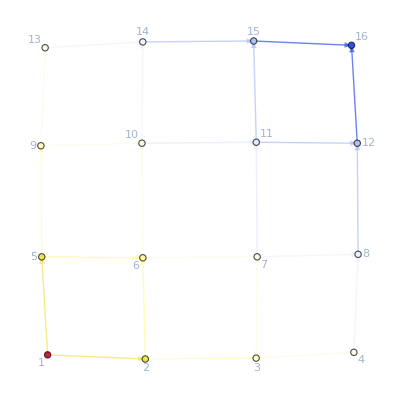

{u1→52/7,u2→52/7,u3→38/7,u4→38/7,u5→30/7,u6→30/7,u7→26/7,u8→38/7,u9→38/7,u10→32/7,u11→32/7,u12→26/7,u13→26/7,u14→22/7,u15→30/7,u16→30/7,u17→26/7,u18→26/7,u19→20/7,u20→20/7,u21→2,u22→26/7,u23→22/7,u24→2,u25→0,u26→52/7,u27→38/7,u28→38/7,u29→30/7,u30→32/7,u31→26/7,u32→26/7,u33→22/7,u34→32/7,u35→30/7,u36→26/7,u37→26/7,u38→22/7,u39→20/7,u40→2,u41→26/7,u42→26/7,u43→20/7,u44→22/7,u45→2,u46→2,u47→0,u48→22/7,u49→2,u50→0,u51→0,u52→52/7,j52→0,j51→0,j50→0,j49→0,j48→0,j47→0,j46→0,j45→0,j44→0,j43→0,j42→0,j41→0,j40→0,j39→0,j38→0,j37→0,j36→0,j35→0,j34→0,j33→0,j32→0,j31→0,j30→0,j29→0,j28→0,j27→0,j26→4,j25→4,j24→2,j23→8/7,j22→4/7,j21→2,j20→6/7,j19→6/7,j18→4/7,j17→6/7,j16→4/7,j15→4/7,j14→8/7,j13→6/7,j12→4/7,j11→6/7,j10→6/7,j9→8/7,j8→6/7,j7→4/7,j6→4/7,j5→4/7,j4→6/7,j3→8/7,j2→2,j1→2}

```mathematica
EqAllAll=Lookup[d2egrid,"EqAllAll",Print["No equations to solve."];
Return[]];
EqCriticalCase=Lookup[d2egrid,"EqCriticalCase",Print["Critical case equations are missing."];
Return[]];
InitRules=Lookup[d2egrid,"BoundaryRules",Print["Need boundary conditions"];];
{system,rules}=CleanEqualities[{EqCriticalCase&&EqAllAll,InitRules}];
vars = Join[Values[d2egrid["uvars"]],Reverse[Values[d2egrid["jvars"]]]];
{time,{{jtsystem,nojtrules},novariables}}=EliminateVars[{{system,rules},vars}]//AbsoluteTiming;
time
ColorNetworkByValueFunctionOperator[d2egrid][nojtrules]
MapThread[Rule,{vars,vars/.nojtrules}]
```